### Working example

```mathematica
eme=3;
ege=3;
ete =1;
gr=GridGraph[{eme,ege,ete},DirectedEdges->True];
```

```mathematica
{timegridata,d2egrid}=AbsoluteTiming@D2E[
AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0},(*SwitchingCostsData=*){}}]
];
timegridata
```

0.346946

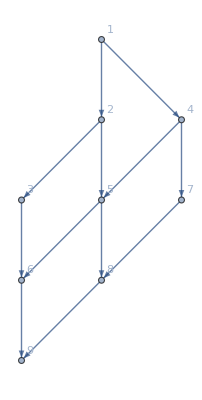
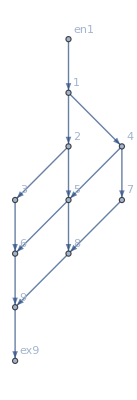
<|Vertices List→{1,2,3,4,5,6,7,8,9},Adjacency Matrix→SparseArray[…],Entrance Vertices and Currents→{{1,4}},Exit Vertices and Terminal Costs→{{9,0}},Switching Costs→{},BG→-Graphics-,InEdges→{en1->1},OutEdges→{9->ex9},FG→-Graphics-,jvars→<|{1,1->2}→j1,{2,1->2}→j2,{1,1->4}→j3,{4,1->4}→j4,{2,2->3}→j5,{3,2->3}→j6,{2,2->5}→j7,{5,2->5}→j8,{3,3->6}→j9,{6,3->6}→j10,{4,4->5}→j11,{5,4->5}→j12,{4,4->7}→j13,{7,4->7}→j14,{5,5->6}→j15,{6,5->6}→j16,{5,5->8}→j17,{8,5->8}→j18,{6,6->9}→j19,{9,6->9}→j20,{7,7->8}→j21,{8,7->8}→j22,{8,8->9}→j23,{9,8->9}→j24,{9,9->ex9}→j25,{ex9,9->ex9}→j26,{en1,en1->1}→j27,{1,en1->1}→j28|>,jtvars→<|{1,1->2,1->4}→jt1,{1,1->2,en1->1}→jt2,{1,1->4,1->2}→jt3,{1,1->4,en1->1}→jt4,{1,en1->1,1->2}→jt5,{1,en1->1,1->4}→jt6,{2,1->2,2->3}→jt7,{2,1->2,2->5}→jt8,{2,2->3,1->2}→jt9,{2,2->3,2->5}→jt10,{2,2->5,1->2}→jt11,{2,2->5,2->3}→jt12,{3,2->3,3->6}→jt13,{3,3->6,2->3}→jt14,{4,1->4,4->5}→jt15,{4,1->4,4->7}→jt16,{4,4->5,1->4}→jt17,{4,4->5,4->7}→jt18,{4,4->7,1->4}→jt19,{4,4->7,4->5}→jt20,{5,2->5,4->5}→jt21,{5,2->5,5->6}→jt22,{5,2->5,5->8}→jt23,{5,4->5,2->5}→jt24,{5,4->5,5->6}→jt25,{5,4->5,5->8}→jt26,{5,5->6,2->5}→jt27,{5,5->6,4->5}→jt28,{5,5->6,5->8}→jt29,{5,5->8,2->5}→jt30,{5,5->8,4->5}→jt31,{5,5->8,5->6}→jt32,{6,3->6,5->6}→jt33,{6,3->6,6->9}→jt34,{6,5->6,3->6}→jt35,{6,5->6,6->9}→jt36,{6,6->9,3->6}→jt37,{6,6->9,5->6}→jt38,{7,4->7,7->8}→jt39,{7,7->8,4->7}→jt40,{8,5->8,7->8}→jt41,{8,5->8,8->9}→jt42,{8,7->8,5->8}→jt43,{8,7->8,8->9}→jt44,{8,8->9,5->8}→jt45,{8,8->9,7->8}→jt46,{9,6->9,8->9}→jt47,{9,6->9,9->ex9}→jt48,{9,8->9,6->9}→jt49,{9,8->9,9->ex9}→jt50,{9,9->ex9,6->9}→jt51,{9,9->ex9,8->9}→jt52|>,uvars→<|{1,1->2}→u1,{2,1->2}→u2,{1,1->4}→u3,{4,1->4}→u4,{2,2->3}→u5,{3,2->3}→u6,{2,2->5}→u7,{5,2->5}→u8,{3,3->6}→u9,{6,3->6}→u10,{4,4->5}→u11,{5,4->5}→u12,{4,4->7}→u13,{7,4->7}→u14,{5,5->6}→u15,{6,5->6}→u16,{5,5->8}→u17,{8,5->8}→u18,{6,6->9}→u19,{9,6->9}→u20,{7,7->8}→u21,{8,7->8}→u22,{8,8->9}→u23,{9,8->9}→u24,{9,9->ex9}→u25,{ex9,9->ex9}→u26,{en1,en1->1}→u27,{1,en1->1}→u28|>,jays→<|1->2→-j1+j2,1->4→-j3+j4,2->3→-j5+j6,2->5→-j7+j8,3->6→j10-j9,4->5→-j11+j12,4->7→-j13+j14,5->6→-j15+j16,5->8→-j17+j18,6->9→-j19+j20,7->8→-j21+j22,8->9→-j23+j24|>,AllOr→(jt1==0||4+jt1-jt15-jt20+jt21+jt28+jt31-jt39+jt40==0)&&(jt16-jt20+jt21+jt28+jt31-jt39+jt40==0||jt15+jt16==0)&&(jt14==0||4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt39+jt40==0)&&(jt24+jt27+jt30==0||jt21+jt22+jt23==0)&&(jt14==0||4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt39+jt40==0)&&(jt21+jt28+jt31==0||jt15+jt20==0)&&(jt40==0||jt39==0)&&(jt27+jt28+jt29==0||jt15+jt20+jt22-jt24-jt26+jt32==0)&&(jt30+jt31+jt32==0||jt23+jt26+jt29==0)&&(jt49==0||4-jt23-jt26-jt29+jt30+jt31+jt32-jt39+jt40+jt49==0)&&(jt40==0||jt39==0)&&(-jt23-jt26-jt29+jt30+jt31+jt32-jt39+jt40+jt42+jt44==0||jt42+jt44==0)&&(jt1==0||jt16-jt20+jt21+jt28+jt31-jt39+jt40==0)&&(jt10==0||-jt1-jt10+jt14+jt24+jt27+jt30==0)&&(jt1+jt10-jt14==0||-jt10+jt21+jt22+jt23==0)&&(4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt39+jt40==0||jt14==0)&&(jt15==0||jt16+jt21+jt28+jt31-jt39==0)&&(jt16==0||-jt20+jt40==0)&&(-jt16+jt39==0||jt20==0)&&(jt21==0||jt24==0)&&(jt22==0||jt27==0)&&(jt23==0||jt30==0)&&(jt15+jt20-jt24-jt26==0||jt28==0)&&(jt26==0||jt31==0)&&(jt29==0||jt32==0)&&(jt27+jt28+jt29+jt37-jt49==0||jt14-jt37==0)&&(4+jt14-jt15-jt20-jt22-jt23+jt24-jt29+jt30+jt31-jt37-jt39+jt40+jt49==0||jt37==0)&&(-jt14+jt15+jt20+jt22-jt24-jt26+jt32+jt37==0||-jt37+jt49==0)&&(jt39==0||jt40==0)&&(jt23+jt26+jt29-jt42==0||jt39-jt44==0)&&(jt42==0||jt30+jt31+jt32-jt39+jt44==0)&&(jt44==0||-jt23-jt26-jt29+jt40+jt42==0)&&(-jt23-jt26-jt29+jt30+jt31+jt32-jt39+jt40+jt42+jt44==0||jt49==0)&&(4+jt1+jt10-jt15-jt20-jt22-jt23+jt28+jt31-jt39+jt40==0||-jt10+jt14==0)&&(4+jt1-jt15-jt16==0||u1-u27==0)&&(-jt1+jt15+jt16==0||u1-u27==0)&&(4-jt42-jt44+jt49==0||-u20==0)&&(jt42+jt44-jt49==0||-u20==0),AllIneq→jt1≥0&&4+jt1-jt15-jt20+jt21+jt28+jt31-jt39+jt40≥0&&jt16-jt20+jt21+jt28+jt31-jt39+jt40≥0&&jt15+jt16≥0&&jt14≥0&&4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt39+jt40≥0&&jt24+jt27+jt30≥0&&jt21+jt22+jt23≥0&&jt14≥0&&4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt39+jt40≥0&&jt21+jt28+jt31≥0&&jt15+jt20≥0&&jt40≥0&&jt39≥0&&jt27+jt28+jt29≥0&&jt15+jt20+jt22-jt24-jt26+jt32≥0&&jt30+jt31+jt32≥0&&jt23+jt26+jt29≥0&&jt49≥0&&4-jt23-jt26-jt29+jt30+jt31+jt32-jt39+jt40+jt49≥0&&jt40≥0&&jt39≥0&&-jt23-jt26-jt29+jt30+jt31+jt32-jt39+jt40+jt42+jt44≥0&&jt42+jt44≥0&&jt1≥0&&jt16-jt20+jt21+jt28+jt31-jt39+jt40≥0&&4+jt1-jt15-jt16≥0&&-jt1+jt15+jt16≥0&&4+jt1+jt10-jt15-jt20-jt22-jt23+jt28+jt31-jt39+jt40≥0&&-jt10+jt21+jt22+jt23≥0&&-jt10+jt14≥0&&jt10≥0&&jt1+jt10-jt14≥0&&-jt1-jt10+jt14+jt24+jt27+jt30≥0&&4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt39+jt40≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt16+jt21+jt28+jt31-jt39≥0&&-jt16+jt39≥0&&-jt20+jt40≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt15+jt20-jt24-jt26≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0&&jt27+jt28+jt29+jt37-jt49≥0&&4+jt14-jt15-jt20-jt22-jt23+jt24-jt29+jt30+jt31-jt37-jt39+jt40+jt49≥0&&jt14-jt37≥0&&-jt14+jt15+jt20+jt22-jt24-jt26+jt32+jt37≥0&&jt37≥0&&-jt37+jt49≥0&&jt39≥0&&jt40≥0&&jt23+jt26+jt29-jt42≥0&&jt42≥0&&jt39-jt44≥0&&jt44≥0&&jt30+jt31+jt32-jt39+jt44≥0&&-jt23-jt26-jt29+jt40+jt42≥0&&-jt23-jt26-jt29+jt30+jt31+jt32-jt39+jt40+jt42+jt44≥0&&4-jt42-jt44+jt49≥0&&jt49≥0&&jt42+jt44-jt49≥0&&u27≤u1&&u20≤0,EqAllAll→(jt1==0||4+jt1-jt15-jt20+jt21+jt28+jt31-jt39+jt40==0)&&(jt16-jt20+jt21+jt28+jt31-jt39+jt40==0||jt15+jt16==0)&&(jt14==0||4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt39+jt40==0)&&(jt24+jt27+jt30==0||jt21+jt22+jt23==0)&&(jt14==0||4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt39+jt40==0)&&(jt21+jt28+jt31==0||jt15+jt20==0)&&(jt40==0||jt39==0)&&(jt27+jt28+jt29==0||jt15+jt20+jt22-jt24-jt26+jt32==0)&&(jt30+jt31+jt32==0||jt23+jt26+jt29==0)&&(jt49==0||4-jt23-jt26-jt29+jt30+jt31+jt32-jt39+jt40+jt49==0)&&(jt40==0||jt39==0)&&(-jt23-jt26-jt29+jt30+jt31+jt32-jt39+jt40+jt42+jt44==0||jt42+jt44==0)&&(jt1==0||jt16-jt20+jt21+jt28+jt31-jt39+jt40==0)&&(jt10==0||-jt1-jt10+jt14+jt24+jt27+jt30==0)&&(jt1+jt10-jt14==0||-jt10+jt21+jt22+jt23==0)&&(4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt39+jt40==0||jt14==0)&&(jt15==0||jt16+jt21+jt28+jt31-jt39==0)&&(jt16==0||-jt20+jt40==0)&&(-jt16+jt39==0||jt20==0)&&(jt21==0||jt24==0)&&(jt22==0||jt27==0)&&(jt23==0||jt30==0)&&(jt15+jt20-jt24-jt26==0||jt28==0)&&(jt26==0||jt31==0)&&(jt29==0||jt32==0)&&(jt27+jt28+jt29+jt37-jt49==0||jt14-jt37==0)&&(4+jt14-jt15-jt20-jt22-jt23+jt24-jt29+jt30+jt31-jt37-jt39+jt40+jt49==0||jt37==0)&&(-jt14+jt15+jt20+jt22-jt24-jt26+jt32+jt37==0||-jt37+jt49==0)&&(jt39==0||jt40==0)&&(jt23+jt26+jt29-jt42==0||jt39-jt44==0)&&(jt42==0||jt30+jt31+jt32-jt39+jt44==0)&&(jt44==0||-jt23-jt26-jt29+jt40+jt42==0)&&(-jt23-jt26-jt29+jt30+jt31+jt32-jt39+jt40+jt42+jt44==0||jt49==0)&&(4+jt1+jt10-jt15-jt20-jt22-jt23+jt28+jt31-jt39+jt40==0||-jt10+jt14==0)&&(4+jt1-jt15-jt16==0||u1-u27==0)&&(-jt1+jt15+jt16==0||u1-u27==0)&&(4-jt42-jt44+jt49==0||-u20==0)&&(jt42+jt44-jt49==0||-u20==0)&&jt1≥0&&4+jt1-jt15-jt20+jt21+jt28+jt31-jt39+jt40≥0&&jt16-jt20+jt21+jt28+jt31-jt39+jt40≥0&&jt15+jt16≥0&&jt14≥0&&4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt39+jt40≥0&&jt24+jt27+jt30≥0&&jt21+jt22+jt23≥0&&jt14≥0&&4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt39+jt40≥0&&jt21+jt28+jt31≥0&&jt15+jt20≥0&&jt40≥0&&jt39≥0&&jt27+jt28+jt29≥0&&jt15+jt20+jt22-jt24-jt26+jt32≥0&&jt30+jt31+jt32≥0&&jt23+jt26+jt29≥0&&jt49≥0&&4-jt23-jt26-jt29+jt30+jt31+jt32-jt39+jt40+jt49≥0&&jt40≥0&&jt39≥0&&-jt23-jt26-jt29+jt30+jt31+jt32-jt39+jt40+jt42+jt44≥0&&jt42+jt44≥0&&jt1≥0&&jt16-jt20+jt21+jt28+jt31-jt39+jt40≥0&&4+jt1-jt15-jt16≥0&&-jt1+jt15+jt16≥0&&4+jt1+jt10-jt15-jt20-jt22-jt23+jt28+jt31-jt39+jt40≥0&&-jt10+jt21+jt22+jt23≥0&&-jt10+jt14≥0&&jt10≥0&&jt1+jt10-jt14≥0&&-jt1-jt10+jt14+jt24+jt27+jt30≥0&&4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt39+jt40≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt16+jt21+jt28+jt31-jt39≥0&&-jt16+jt39≥0&&-jt20+jt40≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt15+jt20-jt24-jt26≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0&&jt27+jt28+jt29+jt37-jt49≥0&&4+jt14-jt15-jt20-jt22-jt23+jt24-jt29+jt30+jt31-jt37-jt39+jt40+jt49≥0&&jt14-jt37≥0&&-jt14+jt15+jt20+jt22-jt24-jt26+jt32+jt37≥0&&jt37≥0&&-jt37+jt49≥0&&jt39≥0&&jt40≥0&&jt23+jt26+jt29-jt42≥0&&jt42≥0&&jt39-jt44≥0&&jt44≥0&&jt30+jt31+jt32-jt39+jt44≥0&&-jt23-jt26-jt29+jt40+jt42≥0&&-jt23-jt26-jt29+jt30+jt31+jt32-jt39+jt40+jt42+jt44≥0&&4-jt42-jt44+jt49≥0&&jt49≥0&&jt42+jt44-jt49≥0&&u27≤u1&&u20≤0,BoundaryRules→<|j2→4+jt1-jt15-jt20+jt21+jt28+jt31-jt39+jt40,j4→jt15+jt16,j27→0,j1→jt1,j6→4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt39+jt40,j8→jt21+jt22+jt23,j5→jt14,j10→4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt39+jt40,j3→jt16-jt20+jt21+jt28+jt31-jt39+jt40,j12→jt15+jt20,j14→jt39,j7→jt24+jt27+jt30,j11→jt21+jt28+jt31,j16→jt15+jt20+jt22-jt24-jt26+jt32,j18→jt23+jt26+jt29,j9→jt14,j15→jt27+jt28+jt29,j20→4-jt23-jt26-jt29+jt30+jt31+jt32-jt39+jt40+jt49,j13→jt40,j22→jt39,j17→jt30+jt31+jt32,j21→jt40,j24→jt42+jt44,j19→jt49,j23→-jt23-jt26-jt29+jt30+jt31+jt32-jt39+jt40+jt42+jt44,j26→4,j28→4,u26→0,u3→u1,u5→u2,u7→u2,u9→u6,u13→u11,u4→u11,u15→u12,u17→u12,u8→u12,u16→u10,u19→u10,u21→u14,u22→u18,u23→u18,u24→u20,jt2→0,jt4→0,jt51→0,jt52→0,u25→0,u28→u27,j25→0,jt11→jt1+jt10-jt14,jt12→-jt1-jt10+jt14+jt24+jt27+jt30,jt13→4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt39+jt40,jt17→jt16+jt21+jt28+jt31-jt39,jt18→-jt16+jt39,jt19→-jt20+jt40,jt25→jt15+jt20-jt24-jt26,jt3→jt16-jt20+jt21+jt28+jt31-jt39+jt40,jt33→jt27+jt28+jt29+jt37-jt49,jt34→4+jt14-jt15-jt20-jt22-jt23+jt24-jt29+jt30+jt31-jt37-jt39+jt40+jt49,jt35→jt14-jt37,jt36→-jt14+jt15+jt20+jt22-jt24-jt26+jt32+jt37,jt38→-jt37+jt49,jt41→jt23+jt26+jt29-jt42,jt43→jt39-jt44,jt45→jt30+jt31+jt32-jt39+jt44,jt46→-jt23-jt26-jt29+jt40+jt42,jt47→-jt23-jt26-jt29+jt30+jt31+jt32-jt39+jt40+jt42+jt44,jt48→4-jt42-jt44+jt49,jt5→4+jt1-jt15-jt16,jt50→jt42+jt44-jt49,jt6→-jt1+jt15+jt16,jt7→4+jt1+jt10-jt15-jt20-jt22-jt23+jt28+jt31-jt39+jt40,jt8→-jt10+jt21+jt22+jt23,jt9→-jt10+jt14|>,InitRules→<|j2→4+jt1-jt15-jt20+jt21+jt28+jt31-jt39+jt40,j4→jt15+jt16,j27→0,j1→jt1,j6→4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt39+jt40,j8→jt21+jt22+jt23,j5→jt14,j10→4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt39+jt40,j3→jt16-jt20+jt21+jt28+jt31-jt39+jt40,j12→jt15+jt20,j14→jt39,j7→jt24+jt27+jt30,j11→jt21+jt28+jt31,j16→jt15+jt20+jt22-jt24-jt26+jt32,j18→jt23+jt26+jt29,j9→jt14,j15→jt27+jt28+jt29,j20→4-jt23-jt26-jt29+jt30+jt31+jt32-jt39+jt40+jt49,j13→jt40,j22→jt39,j17→jt30+jt31+jt32,j21→jt40,j24→jt42+jt44,j19→jt49,j23→-jt23-jt26-jt29+jt30+jt31+jt32-jt39+jt40+jt42+jt44,j26→4,j28→4,u26→0,u3→u1,u5→u2,u7→u2,u9→u6,u13→u11,u4→u11,u15→u12,u17→u12,u8→u12,u16→u10,u19→u10,u21→u14,u22→u18,u23→u18,u24→u20,jt2→0,jt4→0,jt51→0,jt52→0,u25→0,u28→u27,j25→0,jt11→jt1+jt10-jt14,jt12→-jt1-jt10+jt14+jt24+jt27+jt30,jt13→4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt39+jt40,jt17→jt16+jt21+jt28+jt31-jt39,jt18→-jt16+jt39,jt19→-jt20+jt40,jt25→jt15+jt20-jt24-jt26,jt3→jt16-jt20+jt21+jt28+jt31-jt39+jt40,jt33→jt27+jt28+jt29+jt37-jt49,jt34→4+jt14-jt15-jt20-jt22-jt23+jt24-jt29+jt30+jt31-jt37-jt39+jt40+jt49,jt35→jt14-jt37,jt36→-jt14+jt15+jt20+jt22-jt24-jt26+jt32+jt37,jt38→-jt37+jt49,jt41→jt23+jt26+jt29-jt42,jt43→jt39-jt44,jt45→jt30+jt31+jt32-jt39+jt44,jt46→-jt23-jt26-jt29+jt40+jt42,jt47→-jt23-jt26-jt29+jt30+jt31+jt32-jt39+jt40+jt42+jt44,jt48→4-jt42-jt44+jt49,jt5→4+jt1-jt15-jt16,jt50→jt42+jt44-jt49,jt6→-jt1+jt15+jt16,jt7→4+jt1+jt10-jt15-jt20-jt22-jt23+jt28+jt31-jt39+jt40,jt8→-jt10+jt21+jt22+jt23,jt9→-jt10+jt14|>,RulesCriticalCase→<|j2→4+jt1-jt15-jt20+jt21+jt28+(-1+jt15+jt20-jt21-jt28)-jt39+(-1+jt39),j4→jt15+jt16,j27→0,j1→jt1,j6→4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+(-1+jt21+jt22+jt23-jt24-jt27)+(-1+jt15+jt20-jt21-jt28)-jt39+(-1+jt39),j8→jt21+jt22+jt23,j5→jt14,j10→4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+(-1+jt21+jt22+jt23-jt24-jt27)+(-1+jt15+jt20-jt21-jt28)-jt39+(-1+jt39),j3→jt16-jt20+jt21+jt28+(-1+jt15+jt20-jt21-jt28)-jt39+(-1+jt39),j12→jt15+jt20,j14→jt39,j7→jt24+jt27+(-1+jt21+jt22+jt23-jt24-jt27),j11→jt21+jt28+(-1+jt15+jt20-jt21-jt28),j16→jt15+jt20+jt22-jt24-jt26+(1-jt15-jt20-jt22+jt24+jt26+jt27+jt28+jt29),j18→jt23+jt26+jt29,j9→jt14,j15→jt27+jt28+jt29,j20→4-jt23-jt26-jt29+(-1+jt21+jt22+jt23-jt24-jt27)+(-1+jt15+jt20-jt21-jt28)+(1-jt15-jt20-jt22+jt24+jt26+jt27+jt28+jt29)-jt39+(-1+jt39)+jt49,j13→-1+jt39,j22→jt39,j17→(-1+jt21+jt22+jt23-jt24-jt27)+(-1+jt15+jt20-jt21-jt28)+(1-jt15-jt20-jt22+jt24+jt26+jt27+jt28+jt29),j21→-1+jt39,j24→jt42+jt44,j19→jt49,j23→-jt23-jt26-jt29+(-1+jt21+jt22+jt23-jt24-jt27)+(-1+jt15+jt20-jt21-jt28)+(1-jt15-jt20-jt22+jt24+jt26+jt27+jt28+jt29)-jt39+(-1+jt39)+jt42+jt44,j26→4,j28→4,u26→0,u3→u1,u5→-2+u1,u7→-2+u1,u9→-3+u1,u13→-2+u1,u4→-2+u1,u15→-3+u1,u17→-3+u1,u8→-3+u1,u16→-4+u1,u19→-4+u1,u21→-3+u1,u22→-4+u1,u23→-4+u1,u24→-6+u1,jt2→0,jt4→0,jt51→0,jt52→0,u25→0,u28→u27,j25→0,jt11→jt1+jt10-jt14,jt12→-jt1-jt10+jt14+jt24+jt27+(-1+jt21+jt22+jt23-jt24-jt27),jt13→4+jt14-jt15-jt20-jt22-jt23+jt24+jt27+jt28+(-1+jt21+jt22+jt23-jt24-jt27)+(-1+jt15+jt20-jt21-jt28)-jt39+(-1+jt39),jt17→jt16+jt21+jt28+(-1+jt15+jt20-jt21-jt28)-jt39,jt18→-jt16+jt39,jt19→-jt20+(-1+jt39),jt25→jt15+jt20-jt24-jt26,jt3→jt16-jt20+jt21+jt28+(-1+jt15+jt20-jt21-jt28)-jt39+(-1+jt39),jt33→jt27+jt28+jt29+jt37-jt49,jt34→4+jt14-jt15-jt20-jt22-jt23+jt24-jt29+(-1+jt21+jt22+jt23-jt24-jt27)+(-1+jt15+jt20-jt21-jt28)-jt37-jt39+(-1+jt39)+jt49,jt35→jt14-jt37,jt36→-jt14+jt15+jt20+jt22-jt24-jt26+(1-jt15-jt20-jt22+jt24+jt26+jt27+jt28+jt29)+jt37,jt38→-jt37+jt49,jt41→jt23+jt26+jt29-jt42,jt43→jt39-jt44,jt45→(-1+jt21+jt22+jt23-jt24-jt27)+(-1+jt15+jt20-jt21-jt28)+(1-jt15-jt20-jt22+jt24+jt26+jt27+jt28+jt29)-jt39+jt44,jt46→-jt23-jt26-jt29+(-1+jt39)+jt42,jt47→-jt23-jt26-jt29+(-1+jt21+jt22+jt23-jt24-jt27)+(-1+jt15+jt20-jt21-jt28)+(1-jt15-jt20-jt22+jt24+jt26+jt27+jt28+jt29)-jt39+(-1+jt39)+jt42+jt44,jt48→4-jt42-jt44+jt49,jt5→4+jt1-jt15-jt16,jt50→jt42+jt44-jt49,jt6→-jt1+jt15+jt16,jt7→4+jt1+jt10-jt15-jt20-jt22-jt23+jt28+(-1+jt15+jt20-jt21-jt28)-jt39+(-1+jt39),jt8→-jt10+jt21+jt22+jt23,jt9→-jt10+jt14,jt30→-1+jt21+jt22+jt23-jt24-jt27,jt31→-1+jt15+jt20-jt21-jt28,jt32→1-jt15-jt20-jt22+jt24+jt26+jt27+jt28+jt29,jt40→-1+jt39,u10→-4+u1,u11→-2+u1,u12→-3+u1,u14→-3+u1,u18→-4+u1,u2→-2+u1,u20→-6+u1,u6→-3+u1|>,Nlhs→{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24},MinimalTimeRhs→{0,0,0,0,0,0,0,0,0,0,0,0},EqCriticalCase→jt15+jt20+jt39+u1==4+jt21+jt28+jt31+jt40+u2&&jt15+jt20+jt39+u11==jt21+jt28+jt31+jt40+u1&&jt15+jt20+jt22+jt23+jt39+u2==4+jt24+jt27+jt28+jt30+jt31+jt40+u6&&jt21+jt22+jt23+u12==jt24+jt27+jt30+u2&&jt15+jt20+jt22+jt23+jt39+u6==4+jt24+jt27+jt28+jt30+jt31+jt40+u10&&jt15+jt20+u12==jt21+jt28+jt31+u11&&jt39+u14==jt40+u11&&jt15+jt20+jt22+jt32+u10==jt24+jt26+jt27+jt28+jt29+u12&&jt23+jt26+jt29+u18==jt30+jt31+jt32+u12&&jt23+jt26+jt29+jt39+u10==4+jt30+jt31+jt32+jt40+u20&&jt39+u18==jt40+u14&&jt23+jt26+jt29+jt39+u20==jt30+jt31+jt32+jt40+u18,Nrhs→{-j1+j2+IntM[-j1+j2,1->2],-j3+j4+IntM[-j3+j4,1->4],-j5+j6+IntM[-j5+j6,2->3],-j7+j8+IntM[-j7+j8,2->5],j10-j9+IntM[j10-j9,3->6],-j11+j12+IntM[-j11+j12,4->5],-j13+j14+IntM[-j13+j14,4->7],-j15+j16+IntM[-j15+j16,5->6],-j17+j18+IntM[-j17+j18,5->8],-j19+j20+IntM[-j19+j20,6->9],-j21+j22+IntM[-j21+j22,7->8],-j23+j24+IntM[-j23+j24,8->9]}|>

```mathematica
d2egrid
```

```mathematica
d2egrid["EqAllAll"]/.d2egrid["RulesCriticalCase"]
```

(jt1==0||2+jt1==0)&&(-2+jt15+jt16==0||jt15+jt16==0)&&(jt14==0||1+jt14==0)&&(-1+jt21+jt22+jt23==0||jt21+jt22+jt23==0)&&(jt14==0||1+jt14==0)&&(-1+jt15+jt20==0||jt15+jt20==0)&&(-1+jt39==0||jt39==0)&&(jt27+jt28+jt29==0||1+jt27+jt28+jt29==0)&&(-1+jt23+jt26+jt29==0||jt23+jt26+jt29==0)&&(jt49==0||2+jt49==0)&&(-1+jt39==0||jt39==0)&&(-2+jt42+jt44==0||jt42+jt44==0)&&(jt1==0||-2+jt15+jt16==0)&&(jt10==0||-1-jt1-jt10+jt14+jt21+jt22+jt23==0)&&(jt1+jt10-jt14==0||-jt10+jt21+jt22+jt23==0)&&(1+jt14==0||jt14==0)&&(jt15==0||-1+jt15+jt16+jt20-jt39==0)&&(jt16==0||-1-jt20+jt39==0)&&(-jt16+jt39==0||jt20==0)&&(jt21==0||jt24==0)&&(jt22==0||jt27==0)&&(jt23==0||-1+jt21+jt22+jt23-jt24-jt27==0)&&(jt15+jt20-jt24-jt26==0||jt28==0)&&(jt26==0||-1+jt15+jt20-jt21-jt28==0)&&(jt29==0||1-jt15-jt20-jt22+jt24+jt26+jt27+jt28+jt29==0)&&(jt27+jt28+jt29+jt37-jt49==0||jt14-jt37==0)&&(1+jt14-jt27-jt28-jt29-jt37+jt49==0||jt37==0)&&(1-jt14+jt27+jt28+jt29+jt37==0||-jt37+jt49==0)&&(jt39==0||-1+jt39==0)&&(jt23+jt26+jt29-jt42==0||jt39-jt44==0)&&(jt42==0||-1+jt23+jt26+jt29-jt39+jt44==0)&&(jt44==0||-1-jt23-jt26-jt29+jt39+jt42==0)&&(-2+jt42+jt44==0||jt49==0)&&(2+jt1+jt10-jt21-jt22-jt23==0||-jt10+jt14==0)&&(4+jt1-jt15-jt16==0||u1-u27==0)&&(-jt1+jt15+jt16==0||u1-u27==0)&&(4-jt42-jt44+jt49==0||6-u1==0)&&(jt42+jt44-jt49==0||6-u1==0)&&jt1≥0&&2+jt1≥0&&-2+jt15+jt16≥0&&jt15+jt16≥0&&jt14≥0&&1+jt14≥0&&-1+jt21+jt22+jt23≥0&&jt21+jt22+jt23≥0&&jt14≥0&&1+jt14≥0&&-1+jt15+jt20≥0&&jt15+jt20≥0&&-1+jt39≥0&&jt39≥0&&jt27+jt28+jt29≥0&&1+jt27+jt28+jt29≥0&&-1+jt23+jt26+jt29≥0&&jt23+jt26+jt29≥0&&jt49≥0&&2+jt49≥0&&-1+jt39≥0&&jt39≥0&&-2+jt42+jt44≥0&&jt42+jt44≥0&&jt1≥0&&-2+jt15+jt16≥0&&4+jt1-jt15-jt16≥0&&-jt1+jt15+jt16≥0&&2+jt1+jt10-jt21-jt22-jt23≥0&&-jt10+jt21+jt22+jt23≥0&&-jt10+jt14≥0&&jt10≥0&&jt1+jt10-jt14≥0&&-1-jt1-jt10+jt14+jt21+jt22+jt23≥0&&1+jt14≥0&&jt14≥0&&jt15≥0&&jt16≥0&&-1+jt15+jt16+jt20-jt39≥0&&-jt16+jt39≥0&&-1-jt20+jt39≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt15+jt20-jt24-jt26≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&-1+jt21+jt22+jt23-jt24-jt27≥0&&-1+jt15+jt20-jt21-jt28≥0&&1-jt15-jt20-jt22+jt24+jt26+jt27+jt28+jt29≥0&&jt27+jt28+jt29+jt37-jt49≥0&&1+jt14-jt27-jt28-jt29-jt37+jt49≥0&&jt14-jt37≥0&&1-jt14+jt27+jt28+jt29+jt37≥0&&jt37≥0&&-jt37+jt49≥0&&jt39≥0&&-1+jt39≥0&&jt23+jt26+jt29-jt42≥0&&jt42≥0&&jt39-jt44≥0&&jt44≥0&&-1+jt23+jt26+jt29-jt39+jt44≥0&&-1-jt23-jt26-jt29+jt39+jt42≥0&&-2+jt42+jt44≥0&&4-jt42-jt44+jt49≥0&&jt49≥0&&jt42+jt44-jt49≥0&&u27≤u1&&-6+u1≤0

```mathematica
d2egrid["AllOr"]/.d2egrid["RulesCriticalCase"]
```

(jt1==0||2+jt1==0)&&(-2+jt15+jt16==0||jt15+jt16==0)&&(jt14==0||1+jt14==0)&&(-1+jt21+jt22+jt23==0||jt21+jt22+jt23==0)&&(jt14==0||1+jt14==0)&&(-1+jt15+jt20==0||jt15+jt20==0)&&(-1+jt39==0||jt39==0)&&(jt27+jt28+jt29==0||1+jt27+jt28+jt29==0)&&(-1+jt23+jt26+jt29==0||jt23+jt26+jt29==0)&&(jt49==0||2+jt49==0)&&(-1+jt39==0||jt39==0)&&(-2+jt42+jt44==0||jt42+jt44==0)&&(jt1==0||-2+jt15+jt16==0)&&(jt10==0||-1-jt1-jt10+jt14+jt21+jt22+jt23==0)&&(jt1+jt10-jt14==0||-jt10+jt21+jt22+jt23==0)&&(1+jt14==0||jt14==0)&&(jt15==0||-1+jt15+jt16+jt20-jt39==0)&&(jt16==0||-1-jt20+jt39==0)&&(-jt16+jt39==0||jt20==0)&&(jt21==0||jt24==0)&&(jt22==0||jt27==0)&&(jt23==0||-1+jt21+jt22+jt23-jt24-jt27==0)&&(jt15+jt20-jt24-jt26==0||jt28==0)&&(jt26==0||-1+jt15+jt20-jt21-jt28==0)&&(jt29==0||1-jt15-jt20-jt22+jt24+jt26+jt27+jt28+jt29==0)&&(jt27+jt28+jt29+jt37-jt49==0||jt14-jt37==0)&&(1+jt14-jt27-jt28-jt29-jt37+jt49==0||jt37==0)&&(1-jt14+jt27+jt28+jt29+jt37==0||-jt37+jt49==0)&&(jt39==0||-1+jt39==0)&&(jt23+jt26+jt29-jt42==0||jt39-jt44==0)&&(jt42==0||-1+jt23+jt26+jt29-jt39+jt44==0)&&(jt44==0||-1-jt23-jt26-jt29+jt39+jt42==0)&&(-2+jt42+jt44==0||jt49==0)&&(2+jt1+jt10-jt21-jt22-jt23==0||-jt10+jt14==0)&&(4+jt1-jt15-jt16==0||u1-u27==0)&&(-jt1+jt15+jt16==0||u1-u27==0)&&(4-jt42-jt44+jt49==0||6-u1==0)&&(jt42+jt44-jt49==0||6-u1==0)

```mathematica
NewReduce[Simplify[d2egrid["AllIneq"]/.d2egrid["RulesCriticalCase"]]&&SortBy[d2egrid["AllOr"]/.d2egrid["RulesCriticalCase"],Simplify`SimplifyCount]]//AbsoluteTiming
```

{0.714096,(jt1==0&&jt14==0&&jt15==1&&jt16==1&&jt20==0&&jt21==0&&jt22==0&&jt24==0&&jt39==1&&jt49==0&&jt44==1&&jt24==jt29&&jt23==1&&jt28==0&&jt24+jt27==0&&jt42==1&&u27==6&&u1==6&&jt10==0&&jt24+jt26==0&&jt37==0)||(jt1==0&&jt14==0&&jt15==1&&jt16==1&&jt20==0&&jt21==0&&jt24==0&&jt27==0&&jt39==1&&jt49==0&&jt44==1&&jt29==0&&jt23==0&&jt28==0&&jt26==1&&jt42==1&&u27==6&&u1==6&&jt10==0&&jt22==1&&jt37==0)||(jt1==0&&jt14==0&&jt15==1&&jt16==1&&jt20==0&&jt21==0&&0≤jt22≤1&&jt27==0&&jt39==1&&jt49==0&&jt44==1&&jt29==0&&jt22+jt23==1&&jt28==0&&jt22==jt26&&jt42==1&&u27==6&&u1==6&&jt10==0&&jt24==0&&jt37==0)||(jt1==0&&jt14==0&&jt15==1&&jt16==1&&jt20==0&&jt21==0&&jt27==0&&jt39==1&&jt49==0&&jt44==1&&jt29==0&&jt23==0&&jt28==0&&jt26==1&&jt42==1&&u27==6&&u1==6&&jt24==0&&jt10==0&&jt22==1&&jt37==0)||(jt1==0&&jt14==0&&jt15==1&&jt16==1&&jt22==0&&jt24==0&&jt39==1&&jt49==0&&jt20==0&&jt44==1&&jt29==0&&jt23==1&&jt28==0&&jt27==0&&jt42==1&&u27==6&&u1==6&&jt21==0&&jt10==0&&jt26==0&&jt37==0)||(jt1==0&&jt14==0&&jt15==1&&jt16==1&&jt22==0&&jt24==0&&jt39==1&&jt49==0&&jt20==0&&jt44==1&&jt29==0&&jt23==1&&jt28==0&&jt27==0&&jt42==1&&u27==6&&u1==6&&jt26==0&&jt10==0&&jt21==0&&jt37==0)||(jt24==0&&jt22==0&&jt1==0&&jt14==0&&jt49==0&&jt39==1&&jt20==0&&jt16==1&&jt15==1&&jt44==1&&jt29==0&&jt23==1&&jt28==0&&jt27==0&&jt42==1&&u27==6&&u1==6&&jt21==0&&jt10==0&&jt26==0&&jt37==0)||(jt24==0&&jt22==0&&jt1==0&&jt14==0&&jt49==0&&jt39==1&&jt20==0&&jt16==1&&jt15==1&&jt44==1&&jt29==0&&jt23==1&&jt28==0&&jt27==0&&jt42==1&&u27==6&&u1==6&&jt26==0&&jt10==0&&jt21==0&&jt37==0)||(0≤jt22≤1&&jt1==0&&jt14==0&&jt15==1&&jt16==1&&jt24==0&&jt27==0&&jt39==1&&jt49==0&&jt20==0&&jt44==1&&jt29==0&&jt22+jt23==1&&jt28==0&&jt22==jt26&&jt42==1&&u27==6&&u1==6&&jt21==0&&jt10==0&&jt37==0)||(jt21==0&&jt1==0&&jt14==0&&jt15==1&&jt16==1&&jt24==0&&jt27==0&&jt39==1&&jt49==0&&jt20==0&&jt44==1&&jt29==0&&jt23==1&&jt28==0&&jt26==0&&jt42==1&&u27==6&&u1==6&&jt21+jt22==0&&jt10==0&&jt37==0)||(jt1==0&&jt14==0&&jt15==1&&jt16==1&&jt21==0&&jt24==0&&jt27==0&&jt39==1&&jt49==0&&jt20==0&&jt44==1&&jt21==jt29&&jt21+jt23==0&&jt21+jt28==0&&jt26==1&&jt42==1&&u27==6&&u1==6&&jt22==1&&jt10==0&&jt37==0)||(0≤jt22≤1&&jt24==0&&jt27==0&&jt1==0&&jt14==0&&jt49==0&&jt39==1&&jt20==0&&jt16==1&&jt15==1&&jt44==1&&jt29==0&&jt22+jt23==1&&jt28==0&&jt22==jt26&&jt42==1&&u27==6&&u1==6&&jt21==0&&jt10==0&&jt37==0)||(jt21==0&&jt24==0&&jt27==0&&jt1==0&&jt14==0&&jt49==0&&jt39==1&&jt20==0&&jt16==1&&jt15==1&&jt44==1&&jt29==0&&jt23==1&&jt28==0&&jt26==0&&jt42==1&&u27==6&&u1==6&&jt21+jt22==0&&jt10==0&&jt37==0)||(jt21==0&&jt24==0&&jt27==0&&jt1==0&&jt14==0&&jt49==0&&jt39==1&&jt20==0&&jt16==1&&jt15==1&&jt44==1&&jt21==jt29&&jt21+jt23==0&&jt21+jt28==0&&jt26==1&&jt42==1&&u27==6&&u1==6&&jt22==1&&jt10==0&&jt37==0)}

```mathematica
Length@%
```

14

```mathematica
SortBy[d2egrid["AllOr"]/.d2egrid["RulesCriticalCase"],Simplify`SimplifyCount]
```

(jt21==0||jt24==0)&&(jt22==0||jt27==0)&&(jt1==0||2+jt1==0)&&(jt14==0||1+jt14==0)&&(jt14==0||1+jt14==0)&&(1+jt14==0||jt14==0)&&(jt49==0||2+jt49==0)&&(-1+jt39==0||jt39==0)&&(-1+jt39==0||jt39==0)&&(jt39==0||-1+jt39==0)&&(jt1==0||-2+jt15+jt16==0)&&(-2+jt42+jt44==0||jt49==0)&&(-jt16+jt39==0||jt20==0)&&(-2+jt15+jt16==0||jt15+jt16==0)&&(-1+jt15+jt20==0||jt15+jt20==0)&&(-2+jt42+jt44==0||jt42+jt44==0)&&(jt16==0||-1-jt20+jt39==0)&&(jt27+jt28+jt29==0||1+jt27+jt28+jt29==0)&&(-1+jt21+jt22+jt23==0||jt21+jt22+jt23==0)&&(-1+jt23+jt26+jt29==0||jt23+jt26+jt29==0)&&(jt15==0||-1+jt15+jt16+jt20-jt39==0)&&(jt15+jt20-jt24-jt26==0||jt28==0)&&(jt42==0||-1+jt23+jt26+jt29-jt39+jt44==0)&&(-jt1+jt15+jt16==0||u1-u27==0)&&(jt42+jt44-jt49==0||6-u1==0)&&(jt26==0||-1+jt15+jt20-jt21-jt28==0)&&(jt23+jt26+jt29-jt42==0||jt39-jt44==0)&&(jt1+jt10-jt14==0||-jt10+jt21+jt22+jt23==0)&&(jt23==0||-1+jt21+jt22+jt23-jt24-jt27==0)&&(jt27+jt28+jt29+jt37-jt49==0||jt14-jt37==0)&&(jt10==0||-1-jt1-jt10+jt14+jt21+jt22+jt23==0)&&(1-jt14+jt27+jt28+jt29+jt37==0||-jt37+jt49==0)&&(4+jt1-jt15-jt16==0||u1-u27==0)&&(4-jt42-jt44+jt49==0||6-u1==0)&&(jt44==0||-1-jt23-jt26-jt29+jt39+jt42==0)&&(jt29==0||1-jt15-jt20-jt22+jt24+jt26+jt27+jt28+jt29==0)&&(1+jt14-jt27-jt28-jt29-jt37+jt49==0||jt37==0)&&(2+jt1+jt10-jt21-jt22-jt23==0||-jt10+jt14==0)

```mathematica
SortBy[d2egrid["AllOr"]/.d2egrid["RulesCriticalCase"],Max[Simplify`SimplifyCount[#[[1]]],Simplify`SimplifyCount[#[[2]]]]&]
```

(jt21==0||jt24==0)&&(jt22==0||jt27==0)&&(jt1==0||2+jt1==0)&&(jt14==0||1+jt14==0)&&(jt14==0||1+jt14==0)&&(1+jt14==0||jt14==0)&&(jt49==0||2+jt49==0)&&(-1+jt39==0||jt39==0)&&(-1+jt39==0||jt39==0)&&(jt39==0||-1+jt39==0)&&(jt1==0||-2+jt15+jt16==0)&&(-2+jt15+jt16==0||jt15+jt16==0)&&(-1+jt15+jt20==0||jt15+jt20==0)&&(jt27+jt28+jt29==0||1+jt27+jt28+jt29==0)&&(-2+jt42+jt44==0||jt42+jt44==0)&&(-2+jt42+jt44==0||jt49==0)&&(-1+jt21+jt22+jt23==0||jt21+jt22+jt23==0)&&(-1+jt23+jt26+jt29==0||jt23+jt26+jt29==0)&&(-jt16+jt39==0||jt20==0)&&(-jt1+jt15+jt16==0||u1-u27==0)&&(jt42+jt44-jt49==0||6-u1==0)&&(jt1+jt10-jt14==0||-jt10+jt21+jt22+jt23==0)&&(jt16==0||-1-jt20+jt39==0)&&(jt23+jt26+jt29-jt42==0||jt39-jt44==0)&&(jt27+jt28+jt29+jt37-jt49==0||jt14-jt37==0)&&(jt15==0||-1+jt15+jt16+jt20-jt39==0)&&(1-jt14+jt27+jt28+jt29+jt37==0||-jt37+jt49==0)&&(4+jt1-jt15-jt16==0||u1-u27==0)&&(jt15+jt20-jt24-jt26==0||jt28==0)&&(jt42==0||-1+jt23+jt26+jt29-jt39+jt44==0)&&(4-jt42-jt44+jt49==0||6-u1==0)&&(jt26==0||-1+jt15+jt20-jt21-jt28==0)&&(jt23==0||-1+jt21+jt22+jt23-jt24-jt27==0)&&(jt10==0||-1-jt1-jt10+jt14+jt21+jt22+jt23==0)&&(2+jt1+jt10-jt21-jt22-jt23==0||-jt10+jt14==0)&&(jt44==0||-1-jt23-jt26-jt29+jt39+jt42==0)&&(jt29==0||1-jt15-jt20-jt22+jt24+jt26+jt27+jt28+jt29==0)&&(1+jt14-jt27-jt28-jt29-jt37+jt49==0||jt37==0)

```mathematica
NewReduce[Simplify[d2egrid["AllIneq"]/.d2egrid["RulesCriticalCase"]]&&
SortBy[d2egrid["AllOr"]/.d2egrid["RulesCriticalCase"],Max[Simplify`SimplifyCount[#[[1]]],Simplify`SimplifyCount[#[[2]]]]&]
]//AbsoluteTiming
```

{0.554955,(jt24==0&&jt21==0&&jt22==0&&jt1==0&&jt14==0&&jt49==0&&jt39==1&&jt16==1&&jt20==0&&jt24==jt29&&jt44==1&&jt23==1&&jt28==0&&jt15==1&&u27==6&&u1==6&&jt10==0&&jt42==1&&jt37==0&&jt24+jt27==0&&jt24+jt26==0)||(jt24==0&&jt21==0&&jt27==0&&jt1==0&&jt14==0&&jt49==0&&jt39==1&&jt16==1&&jt20==0&&jt29==0&&jt44==1&&jt23==0&&jt28==0&&jt15==1&&u27==6&&u1==6&&jt10==0&&jt42==1&&jt37==0&&jt26==1&&jt22==1)||(0≤jt22≤1&&jt21==0&&jt27==0&&jt1==0&&jt14==0&&jt49==0&&jt39==1&&jt16==1&&jt20==0&&jt29==0&&jt44==1&&jt22+jt23==1&&jt28==0&&jt15==1&&u27==6&&u1==6&&jt10==0&&jt42==1&&jt37==0&&jt22==jt26&&jt24==0)||(jt21==0&&jt27==0&&jt1==0&&jt14==0&&jt49==0&&jt39==1&&jt16==1&&jt20==0&&jt29==0&&jt44==1&&jt23==0&&jt28==0&&jt15==1&&u27==6&&u1==6&&jt10==0&&jt42==1&&jt37==0&&jt26==1&&jt24==0&&jt22==1)||(jt24==0&&jt22==0&&jt1==0&&jt14==0&&jt49==0&&jt39==1&&jt16==1&&jt20==0&&jt29==0&&jt44==1&&jt23==1&&jt28==0&&jt15==1&&u27==6&&u1==6&&jt10==0&&jt42==1&&jt37==0&&jt27==0&&jt21==0&&jt26==0)||(jt1==0&&jt10==0&&jt14==0&&jt15==1&&jt16==1&&jt20==0&&jt21==0&&jt22==0&&jt23==1&&jt24==0&&jt26==0&&jt27==0&&jt28==0&&jt29==0&&jt37==0&&jt39==1&&jt42==1&&jt44==1&&jt49==0&&u1==6&&u27==6)||(jt21==0&&jt24==0&&jt27==0&&jt1==0&&jt14==0&&jt49==0&&jt39==1&&jt16==1&&jt20==0&&jt29==0&&jt44==1&&jt23==1&&jt28==0&&jt15==1&&u27==6&&u1==6&&jt10==0&&jt42==1&&jt37==0&&jt26==0&&jt21+jt22==0)||(0≤jt22≤1&&jt24==0&&jt27==0&&jt1==0&&jt14==0&&jt49==0&&jt39==1&&jt16==1&&jt20==0&&jt29==0&&jt44==1&&jt22+jt23==1&&jt28==0&&jt15==1&&u27==6&&u1==6&&jt10==0&&jt42==1&&jt37==0&&jt22==jt26&&jt21==0)||(jt21==0&&jt24==0&&jt27==0&&jt1==0&&jt14==0&&jt49==0&&jt39==1&&jt16==1&&jt20==0&&jt21==jt29&&jt44==1&&jt21+jt23==0&&jt21+jt28==0&&jt15==1&&u27==6&&u1==6&&jt10==0&&jt42==1&&jt37==0&&jt26==1&&jt22==1)}

```mathematica
%27[[2]]//Simplify
```

jt1==0&&jt10==0&&jt14==0&&jt15==1&&jt16==1&&jt20==0&&jt21==0&&jt24==0&&jt37==0&&jt39==1&&jt42==1&&jt44==1&&jt49==0&&u1==6&&u27==6&&((jt27==0&&((jt22==1&&jt26==1&&((jt21+jt23==0&&jt21+jt28==0&&jt21==jt29)||(jt23==0&&jt28==0&&jt29==0)))||(jt28==0&&jt29==0&&((jt23==1&&jt26==0&&(jt22==0||jt21+jt22==0))||(jt22≤1&&jt22≥0&&jt22+jt23==1&&jt22==jt26)))))||(jt22==0&&jt23==1&&jt24+jt26==0&&jt24+jt27==0&&jt28==0&&jt24==jt29))

```mathematica
CleanEqualitiesOperator[d2egrid][{%31,{}}]
```

And

And

{(jt22==0&&jt23==1&&jt26==0)||(jt22==1&&jt23==0&&jt26==1)||(jt22==jt26&&jt22+jt23==1&&jt22≥0&&jt22≤1),<|jt1→0,jt10→0,jt14→0,jt15→1,jt16→1,jt20→0,jt21→0,jt24→0,jt37→0,jt39→1,jt42→1,jt44→1,jt49→0,u1→6,u27→6,jt27→0,jt28→0,jt29→0|>}

```mathematica
Head@%31
```

And

```mathematica
EqAllAll=Lookup[d2egrid,"EqAllAll",Print["No equations to solve."];
Return[]];
EqCriticalCase=Lookup[d2egrid,"EqCriticalCase",Print["Critical case equations are missing."];
Return[]];
system = EqCriticalCase&&EqAllAll;
rules=Association@Lookup[d2egrid,"BoundaryRules",Print["Need boundary conditions"];];
us=Values@d2egrid["uvars"];
js=Values[d2egrid["jvars"]];
jts=Values[d2egrid["jtvars"]];
```

```mathematica
({s1,r1}=CleanEqualitiesOperator[d2egrid][{system,rules}]);//AbsoluteTiming
({s,r}=NewCleanEqualities[{system, rules}]);//AbsoluteTiming
```

{131.75,Null}

$Aborted

```mathematica
AssociateTo
```

```mathematica
uvars=d2egrid["uvars"];
vl=DeleteDuplicates@(First/@Keys@uvars)
```

{1,2,4,3,5,6,7,8,9,ex9,en1}

```mathematica
Transu2/@TransitionsAt[d2egrid["FG"],#]&/@vl
BooleanConvert[Reduce[#,Reals],"CNF"]&/@%
DeleteCases[%,True]
DeleteCases[getEqual/@%,True]
Solve[#,Reals]&/@%
```

{{u1≤1+u3,u1≤u28,u3≤1+u1,u3≤1+u28,u28≤u1,u28≤u3},{u2≤2+u5,u2≤2+u7,u5≤1+u2,u5≤1+u7,u7≤u2,u7≤2+u5},{u4≤1+u11,u4≤u13,u11≤1+u4,u11≤u13,u13≤2+u4,u13≤1+u11},{u6≤u9,u9≤u6},{u8≤u12,u8≤2+u15,u8≤1+u17,u12≤1+u8,u12≤2+u15,u12≤1+u17,u15≤1+u8,u15≤u12,u15≤2+u17,u17≤2+u8,u17≤u12,u17≤2+u15},{u10≤u16,u10≤2+u19,u16≤2+u10,u16≤u19,u19≤1+u10,u19≤u16},{u14≤2+u21,u21≤2+u14},{u18≤u22,u18≤2+u23,u22≤1+u18,u22≤1+u23,u23≤1+u18,u23≤u22},{u20≤2+u24,u20≤2+u25,u24≤1+u20,u24≤2+u25,u25≤2+u20,u25≤1+u24},{},{}}

{u1==u28&&-1+u3≤u28≤u3,9,True}
 |  |  |  |

{u1==u28&&-1+u3≤u28≤u3,1,5,(u22==u23||-1+u22≤u18≤u22)&&(u22==u23||1)&&(1)&&(-1+u23≤u18≤u22||u23<u22≤1+u23),1}
 |  |  |  |

{u1==u28,u6==u9,u16==u19}

{{{u28→u1}},{{u9→u6}},{{u19→u16}}}

```mathematica
Select[#,Head[#]===Equal&]&/@Select[%398,!TrueQ[#]&]
```

```mathematica
getEqual/@Select[%398,!TrueQ[#]&]
```

{True,True,True,True,u15==u17&&u17==u8,True,True,True,u20==u25&&u24==u25}

```mathematica
Select[%398,!TrueQ[#]&][[4]]
```

-1+u9≤u6≤2+u9

```mathematica
Simplify/@Select[s1,Head[#]=!=Or&]
```

$Aborted

```mathematica
(system=NewReduce[system])//AbsoluteTiming;
%[[1]]
CleanEqualitiesOperator[d2egrid]@Reduce[system,Reals]//AbsoluteTiming
```

41.0421

{14.2606,{((19 jt34==4&&209 jt35==92&&19 jt37==20&&jt38==0)||(209 jt34==136&&jt35==0&&209 jt37==128&&209 jt38==92)||(jt34+jt35==136/209&&jt34+jt37==24/19&&jt34==4/19+jt38&&209 jt38<92&&jt38>0))&&((jt46==0&&11 jt47==4&&19 jt49==24&&jt50==0)||(11 jt46==4&&jt47==0&&209 jt49==188&&11 jt50==4)||(jt46+jt47==4/11&&jt46+jt49==24/19&&jt46==jt50&&11 jt50<4&&jt50>0))&&((jt58==0&&209 jt59==92&&19 jt61==20&&19 jt62==4)||(209 jt58==92&&jt59==0&&209 jt61==128&&209 jt62==136)||(jt58+jt59==92/209&&jt58+jt61==20/19&&4/19+jt58==jt62&&209 jt62<136&&19 jt62>4)),<|j45→0,jt1→0,jt10→0,jt100→0,jt11→0,jt12→0,jt13→248/209,jt14→4/11,jt15→0,jt16→0,jt17→0,jt18→0,jt19→156/209,jt2→0,jt20→92/209,jt21→0,jt22→0,jt23→0,jt24→0,jt25→156/209,jt26→0,jt27→20/19,jt28→156/209,jt29→0,jt3→0,jt30→0,jt31→0,jt32→0,jt33→0,jt36→0,jt39→0,jt4→0,jt40→0,jt41→0,jt42→0,jt43→0,jt45→0,jt48→0,jt5→460/209,jt51→0,jt52→0,jt54→0,jt55→0,jt57→0,jt6→376/209,jt60→0,jt63→0,jt64→0,jt66→0,jt67→0,jt69→0,jt7→324/209,jt70→156/209,jt71→0,jt72→20/19,jt73→0,jt74→0,jt75→156/209,jt76→0,jt77→0,jt78→92/209,jt79→0,jt8→136/209,jt80→156/209,jt81→0,jt82→0,jt83→0,jt84→4/11,jt85→0,jt86→248/209,jt87→0,jt88→0,jt89→0,jt9→0,jt90→136/209,jt91→0,jt92→324/209,jt93→0,jt94→0,jt95→0,jt96→376/209,jt97→0,jt98→460/209,jt99→0,u11→936/209,u15→688/209,u17→28/11,u21→1344/209,u25→1124/209,u29→860/209,u33→596/209,u35→376/209,u37→108/19,u39→1032/209,u41→784/209,u43→460/209,u45→0,u47→1720/209,u48→1720/209,u7→1260/209,jt44→0,jt53→0,jt56→0,jt65→0,jt68→0|>}}

```mathematica
CleanEqualitiesOperator[d2egrid]@Reduce[%[[2]],Reals]//AbsoluteTiming
```

{0.108082,{(jt22==0&&jt23==1&&jt25==1&&jt26==0)||(jt22==1&&jt23==0&&jt25==0&&jt26==1)||(jt22==jt26&&jt22+jt23==1&&jt22+jt25==1&&0<jt26&&jt26<1),<|j25→0,jt1→0,jt10→0,jt11→0,jt12→0,jt13→1,jt14→0,jt15→1,jt16→1,jt17→0,jt18→0,jt19→0,jt2→0,jt20→0,jt21→0,jt24→0,jt27→0,jt28→0,jt3→0,jt30→0,jt31→0,jt33→0,jt34→1,jt35→0,jt36→1,jt37→0,jt38→0,jt39→1,jt4→0,jt40→0,jt41→0,jt42→1,jt43→0,jt44→1,jt45→0,jt46→0,jt47→0,jt48→2,jt49→0,jt5→2,jt50→2,jt51→0,jt52→0,jt6→2,jt7→1,jt8→1,jt9→0,u13→4,u17→3,u19→2,u21→3,u23→2,u25→0,u27→6,u28→6,u7→4,u9→3,jt29→0,jt32→0|>}}

```mathematica
Reduce[%,Reals]
```

((jt26==0&&jt22==0&&jt25==1&&jt23==1)||(0<jt26<1&&jt22==jt26&&jt25==1-jt22&&jt23==1-jt22)||(jt26==1&&jt22==1&&jt25==0&&jt23==0))&&u9==3&&u7==4&&u28==6&&u27==6&&u25==0&&u23==2&&u21==3&&u19==2&&u17==3&&u13==4&&jt9==0&&jt8==1&&jt7==1&&jt6==2&&jt52==0&&jt51==0&&jt50==2&&jt5==2&&jt49==0&&jt48==2&&jt47==0&&jt46==0&&jt45==0&&jt44==1&&jt43==0&&jt42==1&&jt41==0&&jt40==0&&jt4==0&&jt39==1&&jt38==0&&jt37==0&&jt36==1&&jt35==0&&jt34==1&&jt33==0&&jt32==0&&jt31==0&&jt30==0&&jt3==0&&jt29==0&&jt28==0&&jt27==0&&jt24==0&&jt21==0&&jt20==0&&jt2==0&&jt19==0&&jt18==0&&jt17==0&&jt16==1&&jt15==1&&jt14==0&&jt13==1&&jt12==0&&jt11==0&&jt10==0&&jt1==0&&j25==0

```mathematica
Reduce[jt1==jt10/3+jt11/3-jt13/3-jt15/3+jt16/3-jt2/3+jt3/3+jt5/3-(2 jt6)/3+jt7/3/.{jt7->jt3+jt5}]
```

jt1==jt10/3+jt11/3-jt13/3-jt15/3+jt16/3-jt2/3+(2 jt3)/3+(2 jt5)/3-(2 jt6)/3

```mathematica
system/.shortcutsol
```

```mathematica
sol=getNo[js,jts][system]//Solve//First//Quiet//Association
```

<|u81→0,u84→u83|>

```mathematica
sol=Simplify/@Join[rules/.sol,sol]
system=system/.sol;
```

```mathematica
soluj=getNo[jts][system]//Solve//First//Quiet//Association
```

<||>

```mathematica
sol=Join[sol/.soluj,soluj]
system=system/.sol;
```

```mathematica
solujjts=Solve[getEqual[sysu],Reals]//First//Quiet//Association;
```

```mathematica
sol = Simplify/@Join[sol/.solujjts,solujjts]
system=system/.sol;
```

{}

```mathematica
Solve[getEqual[getNo[Complement[Join[us,js,jts],vars]][system]]]
```

{}

```mathematica
vars=Variables[Join[us,js]/.sol];
```

```mathematica
Terminate[Eqs_][{{system_,rules_},vars_}]:=
Module[{newvars=Drop[vars,1], compvars,groups,subsys,subsyscomplement,subsyseq,subsol ,newsol ={}, newsys, us=Values@Eqs["uvars"],js=Values@Eqs["jvars"],newrules},
compvars = Complement[vars,Take[vars,UpTo[3]]];
(*Print[compvars];*)
groups=GroupBy[List@@system,Function[exp,And@@(FreeQ[#][exp]&/@compvars)]](*True is free of compvars, False only has vars*);
subsys=And@@groups[True];
subsys = Simplify@subsys;
Print["simplify\n",subsys];
subsyseq = getEqual@subsys;
If[subsyseq ===True,
(*there are no equalities in subsyseq, try harder!*)
subsys = Reduce[subsys,Reals];
subsyseq = getEqual@subsys;
Print["first if:\n",subsyseq];
If[subsyseq ===True,
(*give up, but keep the work done.*)
Print[subsys,Simplify@subsys];
newsys = subsys&&And@@groups[False],
newsol=First@Solve@subsyseq;
newrules=Simplify/@Join[rules/.#,#]&@(Association@newsol);
newvars = Variables[Join[us,js]/.newrules]
]
(*newsol=First@Solve@subsyseq;
newrules=Simplify/@Join[rules/.#,#]&@(Association@newsol);
newvars = Variables[Join[us,js]/.newrules]*)
,
Print["it pays to just simplify\n",subsyseq];
newsol=First@Solve@subsyseq;
(*Print["it pays\n",newsol];*)
newrules=Simplify/@Join[rules/.#,#]&@(Association@newsol);
newvars = Variables[Join[us,js]/.newrules];
];
Print[newvars];
{{system/.newrules,newrules},newvars}
]
```

```mathematica
system = EqCriticalCase&&EqAllAll;
rules=Lookup[d2egrid,"BoundaryRules",Print["Need boundary conditions"];];
shortcutsol=Join[rules/.#,#]&@(getEqual[system]//Solve//First//Association);
{{ts,tr},tv}=FixedPoint[Terminate[d2egrid],{{system/.shortcutsol, shortcutsol},Variables[Join[us,js]/.shortcutsol]},1];//AbsoluteTiming
```

simplify
jt1==0&&jt10≥0&&jt100≥0&&jt101≥0&&jt102≥0&&jt69≥0&&jt94≥0

it pays
jt1==0

it pays
{jt1→0}

{jt10,jt102,jt103,jt104,jt105,jt106,jt107,jt108,jt109,jt11,jt110,jt111,jt112,jt113,jt117,jt118,jt119,jt12,jt123,jt124,jt125,jt126,jt129,jt13,jt130,jt131,jt132,jt133,jt135,jt136,jt137,jt141,jt142,jt144,jt145,jt147,jt148,jt149,jt15,jt153,jt154,jt156,jt157,jt159,jt16,jt160,jt161,jt165,jt167,jt173,jt175,jt179,jt181,jt185,jt187,jt19,jt21,jt22,jt27,jt28,jt29,jt30,jt33,jt34,jt36,jt37,jt39,jt40,jt41,jt45,jt46,jt48,jt49,jt51,jt52,jt53,jt57,jt58,jt60,jt61,jt63,jt64,jt75,jt77,jt81,jt82,jt84,jt85,jt87,jt88}

{0.064054,Null}

```mathematica
tv
```

{{u1,u2,u3,u4,u5,u6,u7,u8,u9,u10,u11,u12,u13,u14,u15,u16,u17,u18,u19,u20,u21,u22,u23,u24,u25,u26,u27,u28,u29,u30,u31,u32,u33,u34,u35,u36,u37,u38,u39,u40,u41,u42,u43,u44,u45,u46,u47,u48,u49,u50,u51,u52,u53,u54,u55,u56,u57,u58,u59,u60,u61,u62,u63,u64,u65,u66,u67,u68,u69,u70,u71,u72,u73,u74,u75,u76,u77,u78,u79,u80,u81,u82,u83,u84,j1,j2,j3,j4,j5,j6,j7,j8,j9,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j20,j21,j22,j23,j24,j25,j26,j27,j28,j29,j30,j31,j32,j33,j34,j35,j36,j37,j38,j39,j40,j41,j42,j43,j44,j45,j46,j47,j48,j49,j50,j51,j52,j53,j54,j55,j56,j57,j58,j59,j60,j61,j62,j63,j64,j65,j66,j67,j68,j69,j70,j71,j72,j73,j74,j75,j76,j77,j78,j79,j80,j81,j82,j83,j84}/.First[{}]}

```mathematica
Solve[-26/7-jt11-jt12+jt21+jt22+jt27+jt28-jt31==0&&-6/7+jt30+jt33-jt39-jt42==0&&-26/7+jt21+jt22-jt23-jt59-jt60+jt63+jt70-jt71==0&&jt23+jt24+jt27-jt30-jt31-jt33-jt40-jt43==0&&-26/7-jt10+jt11+jt13-jt16+jt28+jt30-jt33-jt34-jt35+jt39+jt40+jt42+jt43-jt47+jt75+jt76-jt79==0&&4-jt102-jt104-jt108+jt15+jt16-jt28-jt31+jt35+jt42+jt43+jt45+jt46-jt51-jt53+jt78+jt81-2 jt87==0&&12/7-jt10+jt101-jt104-jt108+jt11+jt13-jt15-2 jt16-jt33-jt34-jt35+jt39+jt40+jt42+jt43-jt45-jt46-2 jt47+jt51+jt53+2 jt75+jt76+jt82==0&&-32/7-jt10-jt100+jt101+jt102-jt103+jt11+jt13-jt16-jt22-jt24-jt33-jt34-jt35+jt39+jt40+jt42+jt43-jt47+jt57-jt60+jt76+jt78+jt79+jt81+jt82-jt87==0&&60/7+jt100-jt101-jt102+jt11-jt115+jt12+jt22+jt23+2 jt24-jt27-jt28-jt30-jt31+jt35-jt57+jt59+2 jt60-jt63-jt64-jt66-jt67+jt71==0&&6/7+jt11+jt12-jt27-jt28+jt31==-2+jt21+jt22&&jt11+jt12-jt30-jt33+jt39+jt42==jt11+jt12&&jt21+jt23==jt15+jt16&&8/7+jt10-jt11-jt13+jt16-jt42+jt46+jt47+jt51-jt53==4/7+jt10-jt11-jt13+jt16&&4/7+jt15+jt16==4/7+2 jt15+2 jt16&&6/7-jt21+jt23+jt24==jt21+jt22&&jt60+jt63+jt66==jt23+jt24&&4/7+jt15+jt16+jt24==-2+jt21+jt22-jt23&&jt59+jt60-jt63-jt70+jt71==6/7-jt21+jt23+jt24&&jt21+jt22==jt27+jt28&&jt33+jt40+jt43==6/7+jt11+jt12-jt27-jt28+jt30&&2+jt10-jt11-jt13+jt16+jt33+jt34+jt35-jt39-jt40-jt42-jt43+jt47-jt75-jt76+jt79==6/7+jt23+jt24-jt30&&6/7+jt11+jt12==jt33+jt34+jt35&&6/7+jt23+jt24+jt27-jt30-jt31==6/7+jt11+jt12+jt23+jt24-jt27-jt28-jt30-jt31+jt35&&4/7+2 jt15+2 jt16+jt45-jt51-jt53==8/7+jt10-jt11-jt13+jt16&&-2+jt10+jt102+jt104+jt108-jt11-jt13-jt15+jt33+jt34+jt35-jt39-jt40-jt42-jt43-jt45-jt46+jt51+jt53-jt78-jt81+2 jt87==6/7+jt33+jt34+jt35&&8/7+jt10-jt11-jt13+jt16==jt45+jt46+jt47&&6/7+jt23+jt24-jt27+jt33+jt34+jt35-jt42-jt43==8/7+jt10-jt11-jt13+jt16+jt33+jt34+jt35-jt39-jt40-jt42-jt43+jt47&&jt57+jt64+jt67==4/7+jt15+jt16+jt53&&12/7+jt102+jt103+jt104+jt11+jt12-jt22+jt23-jt27-jt28-jt30-jt31+jt35+jt57+jt59-jt63-jt64-jt66-jt67+jt71==4/7+jt15+jt16+2 jt45+2 jt46+2 jt47-jt51-2 jt53&&jt15+jt16+jt22==jt22+jt24+jt59&&jt33+jt34+jt35-jt39+jt45+jt46+jt47-jt51==-4/7+jt22+jt24-jt57+2 jt60&&6/7-jt64-jt67+2 jt69+jt70+jt71==12/7+jt11+jt12+jt23+jt24-jt27-jt28-jt30-jt31+jt35&&jt108+jt114==4/7+jt59+jt60&&-2+jt21+jt22-jt23==jt69+jt70&&-4/7+2 jt22+2 jt24-jt57+jt60-jt66-jt67==6/7+jt11+jt12+jt23+jt24-jt27-jt28-jt30-jt31+jt35-jt66-jt69+jt71&&jt119+jt121==6/7+jt59+jt60-jt63-jt64-jt67+jt69+jt71&&jt28+jt30==jt75+jt76&&jt10-jt101+jt104+jt108-jt11-jt13+jt15+2 jt16+jt33+jt34+jt35-jt39-jt40-jt42-jt43+jt45+jt46+2 jt47-jt51-jt53+jt69+jt70+jt71-jt75-jt76-jt78-jt79-jt82==2+jt10-jt11-jt13+jt16+jt33+jt34+jt35-jt39-jt40-jt42-jt43+jt47-jt75-jt76+jt78&&jt125+jt127==6/7+jt69+jt70+jt71-jt78&&2+jt10-jt11-jt13+jt16-jt28-jt31+jt33+jt34+2 jt35-jt39-jt40==-20/7-jt10+jt101+jt102+jt11+jt13-jt16-jt33-jt34-jt35+jt39+jt40+jt42+jt43-jt47-jt69-jt70-jt71+jt75+jt76+jt78+jt79+jt81+jt82&&6/7+jt69+jt70+jt71+jt75-jt78-jt79==-6/7+jt101+jt102&&jt100+jt103+jt22+jt24-jt57+jt60==16/7-jt10+jt101-jt104-jt108+jt11+jt13+2 jt15+jt16-jt33-jt34-jt35+jt39+jt40+jt42+jt43+2 jt45+2 jt46+jt47-2 jt51-2 jt53-jt69-jt70-jt71+jt75+jt76+jt78+jt79+jt81+jt82-jt87&&jt132+jt135+jt138==-50/7+2 jt102+2 jt104+2 jt108-jt15-jt16-jt45-jt46-jt47+jt51+jt53+jt87&&4/7-jt40-jt43+jt45+jt46+2 jt47+jt53==-8/7-jt100+3 jt22+3 jt24-3 jt57+3 jt60&&-20/7-jt10+jt101+jt102+jt11+jt13-jt16-jt33-jt34-jt35+jt39+jt40+jt42+jt43-jt47+jt76+jt78+jt79+jt81+jt82-jt87==20/7+jt100+jt11+jt12+jt23+jt24-jt27-jt28-jt30-jt31+jt35+jt59+jt60-jt63-jt64-jt66-jt67+jt71&&-6/7+jt101+jt102-jt103+jt115==-8/7+jt101+jt103+jt104&&jt144+jt147+jt150==jt102+jt103+jt104&&16/7+jt11+jt12+jt23+jt24-jt27-jt28-jt30-jt31+jt35-jt57+2 jt59+jt60-jt63-jt64==-4+2 jt102+2 jt104&&16/7+jt100-jt103+jt11+jt12+jt22+jt23+2 jt24-jt27-jt28-jt30-jt31+jt35-jt57+jt59+2 jt60-jt63-jt64-jt66-jt67+jt71==jt102+jt104+jt108&&jt117+jt122==jt113&&jt156+jt159+jt162==jt114+jt115+jt116&&6/7+jt11+jt12+jt23+jt24-jt27-jt28-jt30-jt31+jt35-jt66-jt69+jt70==jt117+jt118&&-36/7-jt101+jt102+jt103+2 jt104+jt108+jt116==jt119+jt120&&jt167+jt169==jt121+jt122&&jt76+jt78==jt123+jt124&&jt129+jt136+jt139==jt125+jt126&&jt172==jt127+jt128&&-26/7-3 jt10+3 jt101+2 jt102-jt104-jt108+3 jt11+3 jt13+jt15-2 jt16-3 jt33-3 jt34-3 jt35+3 jt39+3 jt40+3 jt42+3 jt43+jt45+jt46-2 jt47-jt51-jt53-3 jt69-3 jt70-3 jt71+3 jt75+2 jt76+3 jt78+2 jt79+2 jt81+2 jt82-jt87==jt129+jt130+jt131&&jt123+jt128==jt132+jt133+jt134&&jt141+jt148+jt151==jt135+jt136+jt137&&jt175+jt177==jt138+jt139+jt140&&-24/7-2 jt100+jt101+jt103+jt104-jt11-jt12+2 jt22-jt23+jt24+jt27+jt28+jt30+jt31-jt35-2 jt57-jt59+jt60+jt63+jt64+jt66+jt67-jt71==jt141+jt142+jt143&&jt130+jt133+jt140==jt144+jt145+jt146&&jt153+jt160+jt163==jt147+jt148+jt149&&jt181+jt183==jt150+jt151+jt152&&2+jt102+jt104-jt108+jt113==jt153+jt154+jt155&&jt142+jt145+jt152==jt156+jt157+jt158&&jt165+jt170==jt159+jt160+jt161&&jt187+jt189==jt162+jt163+jt164&&jt118+jt120==jt165+jt166&&jt154+jt157+jt164==jt167+jt168&&jt193+jt195==jt169+jt170&&jt124+jt126==jt171&&jt173+jt178==jt172&&jt131+jt134+jt137==jt173+jt174&&jt171==jt175+jt176&&jt179+jt184==jt177+jt178&&jt143+jt146+jt149==jt179+jt180&&jt174+jt176==jt181+jt182&&jt185+jt190==jt183+jt184&&jt155+jt158+jt161==jt185+jt186&&jt180+jt182==jt187+jt188&&jt191+jt196==jt189+jt190&&jt166+jt168==jt191+jt192&&jt186+jt188==jt193+jt194&&jt195==0&&jt196==0]
```

{}

## Another approach

```mathematica
{system,rules}=CleanEqualities[d2egrid][{EqCriticalCase&&EqAllAll,InitRules}];
vars = Join[Values[d2egrid["uvars"]],Reverse@Values[d2egrid["jvars"]]];
```

u1

j35

j34

j32

j31

j30

j29

j24

j23

j21

j20

j19

j18

j17

j16

j15

j14

j13

j12

j11

j10

j2

Missing[NotFound]

7.65733

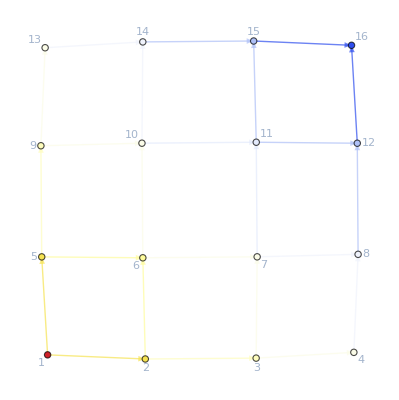

{u1→52/7,u2→52/7,u3→38/7,u4→38/7,u5→30/7,u6→30/7,u7→26/7,u8→38/7,u9→38/7,u10→32/7,u11→32/7,u12→26/7,u13→26/7,u14→22/7,u15→30/7,u16→30/7,u17→26/7,u18→26/7,u19→20/7,u20→20/7,u21→2,u22→26/7,u23→22/7,u24→2,u25→0,u26→52/7,u27→38/7,u28→38/7,u29→30/7,u30→32/7,u31→26/7,u32→26/7,u33→22/7,u34→32/7,u35→30/7,u36→26/7,u37→26/7,u38→22/7,u39→20/7,u40→2,u41→26/7,u42→26/7,u43→20/7,u44→22/7,u45→2,u46→2,u47→0,u48→22/7,u49→2,u50→0,u51→0,u52→52/7,j52→0,j51→0,j50→0,j49→0,j48→0,j47→0,j46→0,j45→0,j44→0,j43→0,j42→0,j41→0,j40→0,j39→0,j38→0,j37→0,j36→0,j35→0,j34→0,j33→0,j32→0,j31→0,j30→0,j29→0,j28→0,j27→0,j26→4,j25→4,j24→2,j23→8/7,j22→4/7,j21→2,j20→6/7,j19→6/7,j18→4/7,j17→6/7,j16→4/7,j15→4/7,j14→8/7,j13→6/7,j12→4/7,j11→6/7,j10→6/7,j9→8/7,j8→6/7,j7→4/7,j6→4/7,j5→4/7,j4→6/7,j3→8/7,j2→2,j1→2}

```mathematica
{time,{{jtsystem,nojtrules},novariables}}=EliminateVars[{{system,rules},vars}]//AbsoluteTiming;
time
ColorNetworkByValueFunctionOperator[d2egrid][nojtrules]
MapThread[Rule,{vars,vars/.nojtrules}]
```

#### Another grid example with different boundary conditions: see way there is a rule like u1->u1.......(this is only for the colornetwork!!!)

```mathematica
eme=10;
ege=10;
ete =1;
gr=GridGraph[{eme,ege,ete},DirectedEdges->True];
{timegridata,d2egrid}=AbsoluteTiming@D2E[
AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{15,I1}/.I1->2000},(*FinalCosts=*){{87,U1}/.U1->0},(*SwitchingCostsData=*){}}]
];
```

```mathematica
EqAllAll=Lookup[d2egrid,"EqAllAll",Print["No equations to solve."];
Return[]];
EqCriticalCase=Lookup[d2egrid,"EqCriticalCase",Print["Critical case equations are missing."];
Return[]];
InitRules=Lookup[d2egrid,"BoundaryRules",Print["Need boundary conditions"];];
{system,rules}=CleanEqualities[{EqCriticalCase&&EqAllAll,InitRules}];
vars = Join[Values[d2egrid["uvars"]],Reverse@Values[d2egrid["jvars"]]];
{time,{{jtsystem,nojtrules},novariables}}=EliminateVars[{{system,rules},vars}]//AbsoluteTiming;
time
ColorNetworkByValueFunctionOperator[d2egrid][nojtrules]
MapThread[Rule,{vars,vars/.nojtrules}]
```

138.107

-Graphics-

{u1→u1,u2→u1,u3→384412993907255/7791295529193+u1,u4→384412993907255/7791295529193+u1,u5→1174630278175040/7791295529193+u1,u6→1174630278175040/7791295529193+u1,u7→2339845131798755/7791295529193+u1,u8→2339845131798755/7791295529193+u1,u9→3427152234995125/7791295529193+u1,u10→3427152234995125/7791295529193+u1,u11→1819130756875000/7791295529193+u1,u12→1819130756875000/7791295529193+u1,u13→155418528268505/7791295529193+u1,u14→155418528268505/7791295529193+u1,u15→-1095880451665960/7791295529193+u1,u16→-1095880451665960/7791295529193+u1,u17→-1900839121066120/7791295529193+u1,u18→-1900839121066120/7791295529193+u1,u19→-763916909407000/2597098509731+u1,u20→-384412993907255/7791295529193+u1,u21→-384412993907255/7791295529193+u1,u22→-21391296453275/7791295529193+u1,u23→-21391296453275/7791295529193+u1,u24→799632708819110/7791295529193+u1,u25→799632708819110/7791295529193+u1,u26→805917627408700/2597098509731+u1,u27→805917627408700/2597098509731+u1,u28→2040826938770540/2597098509731+u1,u29→2040826938770540/2597098509731+u1,u30→624940502453790/2597098509731+u1,u31→624940502453790/2597098509731+u1,u32→-4508679305325/136689395249+u1,u33→-4508679305325/136689395249+u1,u34→-1542220762200265/7791295529193+u1,u35→-1542220762200265/7791295529193+u1,u36→-2314886183311400/7791295529193+u1,u37→-2314886183311400/7791295529193+u1,u38→-1347394442680/3913257423+u1,u39→-1131847685268490/7791295529193+u1,u40→-1131847685268490/7791295529193+u1,u41→-885197894632210/7791295529193+u1,u42→-885197894632210/7791295529193+u1,u43→-372461028671425/7791295529193+u1,u44→-372461028671425/7791295529193+u1,u45→409052871974915/7791295529193+u1,u46→409052871974915/7791295529193+u1,u47→1187605582277885/7791295529193+u1,u48→1187605582277885/7791295529193+u1,u49→-185330823337615/7791295529193+u1,u50→-185330823337615/7791295529193+u1,u51→-1515998155043710/7791295529193+u1,u52→-1515998155043710/7791295529193+u1,u53→-2501121693420175/7791295529193+u1,u54→-2501121693420175/7791295529193+u1,u55→-3133822514603335/7791295529193+u1,u56→-3133822514603335/7791295529193+u1,u57→-19012983948040/43045831653+u1,u58→-3915160529035/14348610551+u1,u59→-3915160529035/14348610551+u1,u60→-671697189378550/2597098509731+u1,u61→-671697189378550/2597098509731+u1,u62→-1813331800847515/7791295529193+u1,u63→-1813331800847515/7791295529193+u1,u64→-145153267993900/708299593563+u1,u65→-145153267993900/708299593563+u1,u66→-1595780535837380/7791295529193+u1,u67→-1595780535837380/7791295529193+u1,u68→-2287752227946005/7791295529193+u1,u69→-2287752227946005/7791295529193+u1,u70→-3120545383013525/7791295529193+u1,u71→-3120545383013525/7791295529193+u1,u72→-3812445341833390/7791295529193+u1,u73→-3812445341833390/7791295529193+u1,u74→-75051440124325/136689395249+u1,u75→-75051440124325/136689395249+u1,u76→-1502521811268835/2597098509731+u1,u77→-17850040046375/43045831653+u1,u78→-17850040046375/43045831653+u1,u79→-3235904409796870/7791295529193+u1,u80→-3235904409796870/7791295529193+u1,u81→-3269088658650085/7791295529193+u1,u82→-3269088658650085/7791295529193+u1,u83→-3386684327021620/7791295529193+u1,u84→-3386684327021620/7791295529193+u1,u85→-1228763183249500/2597098509731+u1,u86→-1228763183249500/2597098509731+u1,u87→-128768247563500/236099864521+u1,u88→-128768247563500/236099864521+u1,u89→-4865985807230995/7791295529193+u1,u90→-4865985807230995/7791295529193+u1,u91→-5350182203813335/7791295529193+u1,u92→-5350182203813335/7791295529193+u1,u93→-514354096191170/708299593563+u1,u94→-514354096191170/708299593563+u1,u95→-305442848407250/410068185747+u1,u96→-4330735168118750/7791295529193+u1,u97→-4330735168118750/7791295529193+u1,u98→-233083166526730/410068185747+u1,u99→-233083166526730/410068185747+u1,u100→-4640434096934335/7791295529193+u1,u101→-4640434096934335/7791295529193+u1,u102→-4994673151754995/7791295529193+u1,u103→-4994673151754995/7791295529193+u1,u104→-96725283623500/136689395249+u1,u105→-96725283623500/136689395249+u1,u106→-2052460364485500/2597098509731+u1,u107→-2052460364485500/2597098509731+u1,u108→-6743863472501620/7791295529193+u1,u109→-6743863472501620/7791295529193+u1,u110→-7064402608086085/7791295529193+u1,u111→-7064402608086085/7791295529193+u1,u112→-7200051821773870/7791295529193+u1,u113→-7200051821773870/7791295529193+u1,u114→-40026419156375/43045831653+u1,u115→-1777589363984835/2597098509731+u1,u116→-1777589363984835/2597098509731+u1,u117→-1835748993727175/2597098509731+u1,u118→-1835748993727175/2597098509731+u1,u119→-5869394413324390/7791295529193+u1,u120→-5869394413324390/7791295529193+u1,u121→-6438233016524525/7791295529193+u1,u122→-6438233016524525/7791295529193+u1,u123→-7215020871198005/7791295529193+u1,u124→-7215020871198005/7791295529193+u1,u125→-8122967565189380/7791295529193+u1,u126→-8122967565189380/7791295529193+u1,u127→-8887684381232900/7791295529193+u1,u128→-8887684381232900/7791295529193+u1,u129→-8963512934255515/7791295529193+u1,u130→-8963512934255515/7791295529193+u1,u131→-2944375917867550/2597098509731+u1,u132→-2944375917867550/2597098509731+u1,u133→-16078968067035/14348610551+u1,u134→-34034928876040/43045831653+u1,u135→-34034928876040/43045831653+u1,u136→-6398245255439335/7791295529193+u1,u137→-6398245255439335/7791295529193+u1,u138→-6891663558657175/7791295529193+u1,u139→-6891663558657175/7791295529193+u1,u140→-7673843629820710/7791295529193+u1,u141→-7673843629820710/7791295529193+u1,u142→-8785541736538615/7791295529193+u1,u143→-8785541736538615/7791295529193+u1,u144→-10231783914870115/7791295529193+u1,u145→-10231783914870115/7791295529193+u1,u146→-11720393552985085/7791295529193+u1,u147→-11720393552985085/7791295529193+u1,u148→-11068836994100425/7791295529193+u1,u149→-11068836994100425/7791295529193+u1,u150→-10438066597981210/7791295529193+u1,u151→-10438066597981210/7791295529193+u1,u152→-10114729360293490/7791295529193+u1,u153→-3390232562680/3913257423+u1,u154→-3390232562680/3913257423+u1,u155→-7033748355355400/7791295529193+u1,u156→-7033748355355400/7791295529193+u1,u157→-7625170936044265/7791295529193+u1,u158→-7625170936044265/7791295529193+u1,u159→-2859978735854175/2597098509731+u1,u160→-2859978735854175/2597098509731+u1,u161→-3340506176755210/2597098509731+u1,u162→-3340506176755210/2597098509731+u1,u163→-4099410934922460/2597098509731+u1,u164→-4099410934922460/2597098509731+u1,u165→-5564422973912300/2597098509731+u1,u166→-5564422973912300/2597098509731+u1,u167→0,u168→-13153374891179890/7791295529193+u1,u169→-13153374891179890/7791295529193+u1,u170→-11735572283928275/7791295529193+u1,u171→-11735572283928275/7791295529193+u1,u172→-189410878347445/132055856427+u1,u173→-2351929538323000/2597098509731+u1,u174→-7361624197642120/7791295529193+u1,u175→-7995335622601960/7791295529193+u1,u176→-8999211734119495/7791295529193+u1,u177→-10422363372194000/7791295529193+u1,u178→-12246359852196875/7791295529193+u1,u179→-1874848405/1042017+u1,u180→-13115821364953960/7791295529193+u1,u181→-12175605824052745/7791295529193+u1,u182→u182,u183→384412993907255/7791295529193+u1,u184→-384412993907255/7791295529193+u1,u185→1174630278175040/7791295529193+u1,u186→-21391296453275/7791295529193+u1,u187→2339845131798755/7791295529193+u1,u188→799632708819110/7791295529193+u1,u189→3427152234995125/7791295529193+u1,u190→805917627408700/2597098509731+u1,u191→1819130756875000/7791295529193+u1,u192→2040826938770540/2597098509731+u1,u193→155418528268505/7791295529193+u1,u194→624940502453790/2597098509731+u1,u195→-1095880451665960/7791295529193+u1,u196→-4508679305325/136689395249+u1,u197→-1900839121066120/7791295529193+u1,u198→-1542220762200265/7791295529193+u1,u199→-763916909407000/2597098509731+u1,u200→-2314886183311400/7791295529193+u1,u201→-1347394442680/3913257423+u1,u202→-21391296453275/7791295529193+u1,u203→-1131847685268490/7791295529193+u1,u204→799632708819110/7791295529193+u1,u205→-885197894632210/7791295529193+u1,u206→805917627408700/2597098509731+u1,u207→-372461028671425/7791295529193+u1,u208→2040826938770540/2597098509731+u1,u209→409052871974915/7791295529193+u1,u210→624940502453790/2597098509731+u1,u211→1187605582277885/7791295529193+u1,u212→-4508679305325/136689395249+u1,u213→-185330823337615/7791295529193+u1,u214→-1542220762200265/7791295529193+u1,u215→-1515998155043710/7791295529193+u1,u216→-2314886183311400/7791295529193+u1,u217→-2501121693420175/7791295529193+u1,u218→-1347394442680/3913257423+u1,u219→-3133822514603335/7791295529193+u1,u220→-19012983948040/43045831653+u1,u221→-885197894632210/7791295529193+u1,u222→-3915160529035/14348610551+u1,u223→-372461028671425/7791295529193+u1,u224→-671697189378550/2597098509731+u1,u225→409052871974915/7791295529193+u1,u226→-1813331800847515/7791295529193+u1,u227→1187605582277885/7791295529193+u1,u228→-145153267993900/708299593563+u1,u229→-185330823337615/7791295529193+u1,u230→-1595780535837380/7791295529193+u1,u231→-1515998155043710/7791295529193+u1,u232→-2287752227946005/7791295529193+u1,u233→-2501121693420175/7791295529193+u1,u234→-3120545383013525/7791295529193+u1,u235→-3133822514603335/7791295529193+u1,u236→-3812445341833390/7791295529193+u1,u237→-19012983948040/43045831653+u1,u238→-75051440124325/136689395249+u1,u239→-1502521811268835/2597098509731+u1,u240→-671697189378550/2597098509731+u1,u241→-17850040046375/43045831653+u1,u242→-1813331800847515/7791295529193+u1,u243→-3235904409796870/7791295529193+u1,u244→-145153267993900/708299593563+u1,u245→-3269088658650085/7791295529193+u1,u246→-1595780535837380/7791295529193+u1,u247→-3386684327021620/7791295529193+u1,u248→-2287752227946005/7791295529193+u1,u249→-1228763183249500/2597098509731+u1,u250→-3120545383013525/7791295529193+u1,u251→-128768247563500/236099864521+u1,u252→-3812445341833390/7791295529193+u1,u253→-4865985807230995/7791295529193+u1,u254→-75051440124325/136689395249+u1,u255→-5350182203813335/7791295529193+u1,u256→-1502521811268835/2597098509731+u1,u257→-514354096191170/708299593563+u1,u258→-305442848407250/410068185747+u1,u259→-3235904409796870/7791295529193+u1,u260→-4330735168118750/7791295529193+u1,u261→-3269088658650085/7791295529193+u1,u262→-233083166526730/410068185747+u1,u263→-3386684327021620/7791295529193+u1,u264→-4640434096934335/7791295529193+u1,u265→-1228763183249500/2597098509731+u1,u266→-4994673151754995/7791295529193+u1,u267→-128768247563500/236099864521+u1,u268→-96725283623500/136689395249+u1,u269→-4865985807230995/7791295529193+u1,u270→-2052460364485500/2597098509731+u1,u271→-5350182203813335/7791295529193+u1,u272→-6743863472501620/7791295529193+u1,u273→-514354096191170/708299593563+u1,u274→-7064402608086085/7791295529193+u1,u275→-305442848407250/410068185747+u1,u276→-7200051821773870/7791295529193+u1,u277→-40026419156375/43045831653+u1,u278→-233083166526730/410068185747+u1,u279→-1777589363984835/2597098509731+u1,u280→-4640434096934335/7791295529193+u1,u281→-1835748993727175/2597098509731+u1,u282→-4994673151754995/7791295529193+u1,u283→-5869394413324390/7791295529193+u1,u284→-96725283623500/136689395249+u1,u285→-6438233016524525/7791295529193+u1,u286→-2052460364485500/2597098509731+u1,u287→-7215020871198005/7791295529193+u1,u288→-6743863472501620/7791295529193+u1,u289→-8122967565189380/7791295529193+u1,u290→-7064402608086085/7791295529193+u1,u291→-8887684381232900/7791295529193+u1,u292→-7200051821773870/7791295529193+u1,u293→-8963512934255515/7791295529193+u1,u294→-40026419156375/43045831653+u1,u295→-2944375917867550/2597098509731+u1,u296→-16078968067035/14348610551+u1,u297→-1835748993727175/2597098509731+u1,u298→-34034928876040/43045831653+u1,u299→-5869394413324390/7791295529193+u1,u300→-6398245255439335/7791295529193+u1,u301→-6438233016524525/7791295529193+u1,u302→-6891663558657175/7791295529193+u1,u303→-7215020871198005/7791295529193+u1,u304→-7673843629820710/7791295529193+u1,u305→-8122967565189380/7791295529193+u1,u306→-8785541736538615/7791295529193+u1,u307→-8887684381232900/7791295529193+u1,u308→-10231783914870115/7791295529193+u1,u309→-8963512934255515/7791295529193+u1,u310→-11720393552985085/7791295529193+u1,u311→-2944375917867550/2597098509731+u1,u312→-11068836994100425/7791295529193+u1,u313→-16078968067035/14348610551+u1,u314→-10438066597981210/7791295529193+u1,u315→-10114729360293490/7791295529193+u1,u316→-6398245255439335/7791295529193+u1,u317→-3390232562680/3913257423+u1,u318→-6891663558657175/7791295529193+u1,u319→-7033748355355400/7791295529193+u1,u320→-7673843629820710/7791295529193+u1,u321→-7625170936044265/7791295529193+u1,u322→-8785541736538615/7791295529193+u1,u323→-2859978735854175/2597098509731+u1,u324→-10231783914870115/7791295529193+u1,u325→-3340506176755210/2597098509731+u1,u326→-11720393552985085/7791295529193+u1,u327→-4099410934922460/2597098509731+u1,u328→-11068836994100425/7791295529193+u1,u329→-5564422973912300/2597098509731+u1,u330→-10438066597981210/7791295529193+u1,u331→-13153374891179890/7791295529193+u1,u332→-10114729360293490/7791295529193+u1,u333→-11735572283928275/7791295529193+u1,u334→-189410878347445/132055856427+u1,u335→-7033748355355400/7791295529193+u1,u336→-2351929538323000/2597098509731+u1,u337→-7625170936044265/7791295529193+u1,u338→-7361624197642120/7791295529193+u1,u339→-2859978735854175/2597098509731+u1,u340→-7995335622601960/7791295529193+u1,u341→-3340506176755210/2597098509731+u1,u342→-8999211734119495/7791295529193+u1,u343→-4099410934922460/2597098509731+u1,u344→-10422363372194000/7791295529193+u1,u345→-5564422973912300/2597098509731+u1,u346→-12246359852196875/7791295529193+u1,u347→-13153374891179890/7791295529193+u1,u348→-1874848405/1042017+u1,u349→0,u350→-11735572283928275/7791295529193+u1,u351→-13115821364953960/7791295529193+u1,u352→-189410878347445/132055856427+u1,u353→-12175605824052745/7791295529193+u1,u354→-212888132000/142065451+u1,u355→-7361624197642120/7791295529193+u1,u356→-7995335622601960/7791295529193+u1,u357→-8999211734119495/7791295529193+u1,u358→-10422363372194000/7791295529193+u1,u359→-12246359852196875/7791295529193+u1,u360→-1874848405/1042017+u1,u361→-13115821364953960/7791295529193+u1,u362→-12175605824052745/7791295529193+u1,u363→-212888132000/142065451+u1,u364→u182,j364→0,j363→500182000776745/7791295529193,j362→16495009489495/136689395249,j361→300887338225095/2597098509731,j360→0,j359→0,j358→0,j357→0,j356→0,j355→0,j354→0,j353→0,j352→4555532206740/63343866091,j351→1137985643210/236099864521,j350→1417802607251615/7791295529193,j349→0,j348→2674785542107655/7791295529193,j347→3539894030557010/7791295529193,j346→4715722960955/708299593563,j345→0,j344→0,j343→0,j342→0,j341→0,j340→0,j339→0,j338→0,j337→0,j336→0,j335→0,j334→0,j333→0,j332→107779079229240/2597098509731,j331→0,j330→19114254427855/236099864521,j329→0,j328→19744138148020/236099864521,j327→0,j326→0,j325→0,j324→0,j323→0,j322→0,j321→0,j320→0,j319→0,j318→0,j317→0,j316→0,j315→0,j314→0,j313→34082697734215/2597098509731,j312→0,j311→130385180652865/7791295529193,j310→0,j309→0,j308→0,j307→0,j306→0,j305→0,j304→0,j303→0,j302→0,j301→0,j300→0,j299→0,j298→0,j297→0,j296→0,j295→0,j294→0,j293→0,j292→0,j291→0,j290→0,j289→0,j288→0,j287→0,j286→0,j285→0,j284→0,j283→0,j282→0,j281→0,j280→0,j279→0,j278→0,j277→0,j276→0,j275→0,j274→0,j273→0,j272→0,j271→0,j270→0,j269→0,j268→0,j267→0,j266→0,j265→0,j264→0,j263→0,j262→0,j261→0,j260→0,j259→0,j258→0,j257→0,j256→0,j255→0,j254→0,j253→0,j252→0,j251→0,j250→0,j249→0,j248→0,j247→0,j246→301804031840/2597098509731,j245→0,j244→216645852914615/7791295529193,j243→0,j242→201759767288135/7791295529193,j241→0,j240→36946866376785/2597098509731,j239→0,j238→0,j237→0,j236→0,j235→0,j234→0,j233→0,j232→0,j231→0,j230→0,j229→0,j228→0,j227→259517570100990/2597098509731,j226→0,j225→260504633548780/2597098509731,j224→0,j223→170912288653595/2597098509731,j222→0,j221→82216596878760/2597098509731,j220→0,j219→0,j218→0,j217→0,j216→0,j215→0,j214→0,j213→0,j212→0,j211→0,j210→0,j209→0,j208→1234909311361840/2597098509731,j207→0,j206→147101833946090/708299593563,j205→0,j204→821024005272385/7791295529193,j203→0,j202→2951395914260/63343866091,j201→0,j200→0,j199→0,j198→0,j197→0,j196→0,j195→0,j194→55690750486370/7791295529193,j193→0,j192→2695328581316495/7791295529193,j191→0,j190→77907750427345/7791295529193,j189→1087307103196370/7791295529193,j188→0,j187→388404951207905/2597098509731,j186→0,j185→1260314647955/12426308659,j184→0,j183→384412993907255/7791295529193,j182→2000,j181→0,j180→0,j179→0,j178→1772123527432370/7791295529193,j177→607998826667625/2597098509731,j176→74902717793395/410068185747,j175→334625370505845/2597098509731,j174→211237141653280/2597098509731,j173→305835582673120/7791295529193,j172→500182000776745/7791295529193,j171→7458195595330/132055856427,j170→0,j169→0,j168→0,j167→2000,j166→0,j165→0,j164→0,j163→133182912635440/236099864521,j162→400844841928370/7791295529193,j161→758904758167250/2597098509731,j160→419275526556970/7791295529193,j159→43684312809185/236099864521,j158→123388228852565/2597098509731,j157→954765271518260/7791295529193,j156→327875842286720/7791295529193,j155→591422580688865/7791295529193,j154→305835582673120/7791295529193,j153→94598441019840/2597098509731,j152→5859184874065/43045831653,j151→7168539701365/43045831653,j150→0,j149→3838927987255/14348610551,j148→0,j147→1446023660585/2265570087,j146→0,j145→11416844695565/43045831653,j144→496203212704990/2597098509731,j143→6828601070315/43045831653,j142→1068915135500/5758533281,j141→5006036341115/43045831653,j140→370566035572635/2597098509731,j139→1350842315630/14348610551,j138→23702426398895/236099864521,j137→3511066850365/43045831653,j136→14952069794480/236099864521,j135→55214056160/729590367,j134→79307709625365/2597098509731,j133→125804518172135/708299593563,j132→1604938844378560/7791295529193,j131→0,j130→701774686614970/2597098509731,j129→0,j128→257519015613835/708299593563,j127→75828553022615/7791295529193,j126→2108816349680735/7791295529193,j125→254905605347840/2597098509731,j124→1570520865340610/7791295529193,j123→302648897997125/2597098509731,j122→1235610613296185/7791295529193,j121→258929284891160/2597098509731,j120→340756381777595/2597098509731,j119→568838603200135/7791295529193,j118→890998274257810/7791295529193,j117→362147432142865/7791295529193,j116→827554034608735/7791295529193,j115→58159629742340/2597098509731,j114→139160763470/729590367,j113→9022518960380/43045831653,j112→4066367775455/708299593563,j111→317949158910/1304419141,j110→45216404562595/2597098509731,j109→11844314412880/43045831653,j108→5623493606745/136689395249,j107→10859593766480/43045831653,j106→586482379045120/7791295529193,j105→854685939055/3913257423,j104→214679975639000/2597098509731,j103→419761519270/2265570087,j102→518668014784505/7791295529193,j101→2263278667385/14348610551,j100→118079684940220/2597098509731,j99→5959485177755/43045831653,j98→70617977642155/2597098509731,j97→5536093501855/43045831653,j96→97844995889120/7791295529193,j95→480455915855375/2597098509731,j94→514052254557000/2597098509731,j93→145519061634880/7791295529193,j92→1266977386750/5758533281,j91→102570951429845/2597098509731,j90→625959221756875/2597098509731,j89→161398798860780/2597098509731,j88→636009641287000/2597098509731,j87→616633637635495/7791295529193,j86→609017205597000/2597098509731,j85→187687539949000/2597098509731,j84→535996274911125/2597098509731,j83→299605222726880/7791295529193,j82→1013559082250/5758533281,j81→2063081901255/136689395249,j80→397558584737000/2597098509731,j79→11061416284405/2597098509731,j78→366625973241625/2597098509731,j77→5047161402995/7791295529193,j76→7159385005145/43045831653,j75→7624104812245/43045831653,j74→76544448906660/2597098509731,j73→257447992965/1304419141,j72→465486745253135/7791295529193,j71→507543013730/2265570087,j70→691899958819865/7791295529193,j69→10837568738395/43045831653,j68→277597718355840/2597098509731,j67→1049979414320/3913257423,j66→230657230702875/2597098509731,j65→9889493807120/43045831653,j64→0,j63→2680951855990/14348610551,j62→0,j61→6744822329620/43045831653,j60→0,j59→103467092530/729590367,j58→0,j57→1066215339211265/7791295529193,j56→1144109572483190/7791295529193,j55→102509193330635/2597098509731,j54→437107882804405/2597098509731,j53→210900273727720/2597098509731,j52→1604547227969815/7791295529193,j51→328374512792155/2597098509731,j50→2102421404608390/7791295529193,j49→443555777235365/2597098509731,j48→2783386118115265/7791295529193,j47→1014734963500/5758533281,j46→2005738819907815/7791295529193,j45→0,j44→480290257392030/2597098509731,j43→0,j42→1129893673503440/7791295529193,j41→0,j40→994084481997515/7791295529193,j39→0,j38→71044831840/729590367,j37→4524510117635/43045831653,j36→122592050688160/2597098509731,j35→1765931733370/14348610551,j34→772665421111135/7791295529193,j33→6955820080885/43045831653,j32→1285226041796740/7791295529193,j31→11382057075685/43045831653,j30→710605409254965/2597098509731,j29→27264504055435/43045831653,j28→1415886436316750/2597098509731,j27→584094216415/2265570087,j26→0,j25→2158552002745/14348610551,j24→0,j23→4772412144635/43045831653,j22→0,j21→4129473432935/43045831653,j20→0,j19→390911607154880/7791295529193,j18→414047062245280/7791295529193,j17→390911607154880/7791295529193,j16→13525463955585/236099864521,j15→24392686951520/236099864521,j14→412413248672030/7791295529193,j13→37918150907105/236099864521,j12→0,j11→87563801505605/410068185747,j10→0,j9→536007159373375/2597098509731,j8→0,j7→0,j6→124999189785310/2597098509731,j5→0,j4→6878038819670/132055856427,j3→0,j2→384412993907255/7791295529193,j1→0}

```mathematica
Simplify/@Select[nojtrules,FreeQ[Symbol]]
```

<|j182→2000,u349→0,j167→2000,j173→305835582673120/7791295529193,j181→0,j183→384412993907255/7791295529193,j184→0,j19→390911607154880/7791295529193,j192→2695328581316495/7791295529193,j193→0,j194→55690750486370/7791295529193,j195→0,j196→0,j197→0,j198→0,j199→0,j2→384412993907255/7791295529193,j200→0,j201→0,j202→2951395914260/63343866091,j21→4129473432935/43045831653,j22→0,j23→4772412144635/43045831653,j24→0,j25→2158552002745/14348610551,j26→0,j27→584094216415/2265570087,j28→1415886436316750/2597098509731,j282→0,j283→0,j284→0,j285→0,j286→0,j287→0,j288→0,j289→0,j29→27264504055435/43045831653,j290→0,j291→0,j292→0,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,j299→0,j3→0,j30→710605409254965/2597098509731,j300→0,j301→0,j302→0,j303→0,j304→0,j305→0,j306→0,j307→0,j308→0,j309→0,j31→11382057075685/43045831653,j310→0,j311→130385180652865/7791295529193,j312→0,j313→34082697734215/2597098509731,j314→0,j315→0,j316→0,j317→0,j318→0,j319→0,j32→1285226041796740/7791295529193,j320→0,j321→0,j322→0,j323→0,j324→0,j325→0,j326→0,j327→0,j328→19744138148020/236099864521,j329→0,j33→6955820080885/43045831653,j330→19114254427855/236099864521,j331→0,j332→107779079229240/2597098509731,j333→0,j334→0,j335→0,j336→0,j337→0,j338→0,j339→0,j34→772665421111135/7791295529193,j340→0,j341→0,j342→0,j343→0,j344→0,j345→0,j346→4715722960955/708299593563,j347→3539894030557010/7791295529193,j348→2674785542107655/7791295529193,j349→0,j35→1765931733370/14348610551,j350→1417802607251615/7791295529193,j351→1137985643210/236099864521,j352→4555532206740/63343866091,j353→0,j354→0,j355→0,j356→0,j357→0,j358→0,j359→0,j36→122592050688160/2597098509731,j360→0,j361→300887338225095/2597098509731,j362→16495009489495/136689395249,j363→500182000776745/7791295529193,j364→0,j37→4524510117635/43045831653,j38→71044831840/729590367,j39→0,j4→6878038819670/132055856427,j40→994084481997515/7791295529193,j41→0,j42→1129893673503440/7791295529193,j43→0,j44→480290257392030/2597098509731,j45→0,j46→2005738819907815/7791295529193,j47→1014734963500/5758533281,j48→2783386118115265/7791295529193,j49→443555777235365/2597098509731,j5→0,j50→2102421404608390/7791295529193,j51→328374512792155/2597098509731,j52→1604547227969815/7791295529193,j53→210900273727720/2597098509731,j54→437107882804405/2597098509731,j55→102509193330635/2597098509731,j56→1144109572483190/7791295529193,j57→1066215339211265/7791295529193,j58→0,j59→103467092530/729590367,j6→124999189785310/2597098509731,j60→0,j61→6744822329620/43045831653,j62→0,j63→2680951855990/14348610551,j64→0,j65→9889493807120/43045831653,j66→230657230702875/2597098509731,j67→1049979414320/3913257423,j68→277597718355840/2597098509731,j69→10837568738395/43045831653,j7→0,j70→691899958819865/7791295529193,j71→507543013730/2265570087,j72→465486745253135/7791295529193,j73→257447992965/1304419141,j74→76544448906660/2597098509731,j75→7624104812245/43045831653,j76→7159385005145/43045831653,j77→5047161402995/7791295529193,j78→366625973241625/2597098509731,j79→11061416284405/2597098509731,j8→0,j80→397558584737000/2597098509731,j81→2063081901255/136689395249,j82→1013559082250/5758533281,j83→299605222726880/7791295529193,j84→535996274911125/2597098509731,j85→187687539949000/2597098509731,j86→609017205597000/2597098509731,j87→616633637635495/7791295529193,j88→636009641287000/2597098509731,j89→161398798860780/2597098509731,j9→536007159373375/2597098509731,j90→625959221756875/2597098509731,j91→102570951429845/2597098509731,j92→1266977386750/5758533281,j93→145519061634880/7791295529193,j94→514052254557000/2597098509731,j95→480455915855375/2597098509731,j96→97844995889120/7791295529193,j97→5536093501855/43045831653,j98→70617977642155/2597098509731,j99→5959485177755/43045831653,jt1→384412993907255/7791295529193,jt102→0,jt105→-jt103-jt104,jt106→0,jt109→-jt107-jt108,jt11→1260314647955/12426308659,jt110→0,jt111→2695328581316495/7791295529193+jt100+jt101-jt103-jt107,jt114→12887262477069505/7791295529193-jt100-jt101+jt103+jt107-jt112-jt113,jt117→-jt115-jt116,jt12→124999189785310/2597098509731,jt120→1415886436316750/2597098509731-jt118-jt119,jt122→198864270750115/708299593563-jt115-jt116-jt118-jt119-jt121,jt123→-198864270750115/708299593563+jt115+jt116+jt118+jt119,jt124→55690750486370/7791295529193-jt118-jt121,jt125→-198864270750115/708299593563+jt116+jt118+jt119+jt121,jt126→710605409254965/2597098509731-jt116-jt119,jt129→412413248672030/7791295529193-jt127-jt128,jt13→0,jt132→710605409254965/2597098509731-jt130-jt131,jt134→1285226041796740/7791295529193-jt127-jt128-jt130-jt131-jt133,jt135→-1285226041796740/7791295529193+jt127+jt128+jt130+jt131,jt136→-jt130-jt133,jt137→-1285226041796740/7791295529193+jt128+jt130+jt131+jt133,jt138→1285226041796740/7791295529193-jt128-jt131,jt14→0,jt141→13525463955585/236099864521-jt139-jt140,jt144→1285226041796740/7791295529193-jt142-jt143,jt146→772665421111135/7791295529193-jt139-jt140-jt142-jt143-jt145,jt147→-772665421111135/7791295529193+jt139+jt140+jt142+jt143,jt148→-jt142-jt145,jt149→-772665421111135/7791295529193+jt140+jt142+jt143+jt145,jt150→772665421111135/7791295529193-jt140-jt143,jt153→414047062245280/7791295529193-jt151-jt152,jt156→772665421111135/7791295529193-jt154-jt155,jt158→122592050688160/2597098509731-jt151-jt152-jt154-jt155-jt157,jt159→-122592050688160/2597098509731+jt151+jt152+jt154+jt155,jt16→0,jt160→-jt154-jt157,jt161→-122592050688160/2597098509731+jt152+jt154+jt155+jt157,jt162→122592050688160/2597098509731-jt152-jt155,jt164→390911607154880/7791295529193,jt165→0,jt166→122592050688160/2597098509731,jt167→0,jt168→0,jt17→1087307103196370/7791295529193,jt170→4129473432935/43045831653,jt171→0,jt172→82216596878760/2597098509731,jt173→0,jt174→0,jt177→4772412144635/43045831653-jt175-jt176,jt18→0,jt180→-jt178-jt179,jt182→82216596878760/2597098509731-jt175-jt176-jt178-jt179-jt181,jt183→88695691774835/2597098509731+jt175+jt176+jt178+jt179,jt184→-jt178-jt181,jt185→jt176+jt178+jt179+jt181,jt186→-jt176-jt179,jt189→2158552002745/14348610551-jt187-jt188,jt19→77907750427345/7791295529193,jt192→-jt190-jt191,jt194→170912288653595/2597098509731-jt187-jt188-jt190-jt191-jt193,jt195→198652649435/5758533281+jt187+jt188+jt190+jt191,jt196→-jt190-jt193,jt197→jt188+jt190+jt191+jt193,jt198→-jt188-jt191,jt2→0,jt20→0,jt201→584094216415/2265570087-jt199-jt200,jt204→-jt202-jt203,jt206→260504633548780/2597098509731-jt199-jt200-jt202-jt203-jt205,jt207→-987063447790/2597098509731+jt199+jt200+jt202+jt203,jt208→-jt202-jt205,jt209→jt200+jt202+jt203+jt205,jt210→-jt200-jt203,jt213→27264504055435/43045831653-jt211-jt212,jt216→-jt214-jt215,jt218→717163038639490/2597098509731-jt211-jt212-jt214-jt215-jt217,jt219→-717163038639490/2597098509731+jt211+jt212+jt214+jt215,jt22→0,jt220→-jt214-jt217,jt221→-1014734963500/5758533281+jt212+jt214+jt215+jt217,jt222→1014734963500/5758533281-jt212-jt215,jt225→11382057075685/43045831653-jt223-jt224,jt228→1014734963500/5758533281-jt226-jt227,jt23→0,jt230→443555777235365/2597098509731-jt223-jt224-jt226-jt227-jt229,jt231→-443555777235365/2597098509731+jt223+jt224+jt226+jt227,jt232→-jt226-jt229,jt233→-443555777235365/2597098509731+jt224+jt226+jt227+jt229,jt234→443555777235365/2597098509731-jt224-jt227,jt237→6955820080885/43045831653-jt235-jt236,jt24→0,jt240→443555777235365/2597098509731-jt238-jt239,jt242→328374512792155/2597098509731-jt235-jt236-jt238-jt239-jt241,jt243→-328374512792155/2597098509731+jt235+jt236+jt238+jt239,jt244→-jt238-jt241,jt245→-328374512792155/2597098509731+jt236+jt238+jt239+jt241,jt246→328374512792155/2597098509731-jt236-jt239,jt249→1765931733370/14348610551-jt247-jt248,jt25→1087307103196370/7791295529193,jt252→328374512792155/2597098509731-jt250-jt251,jt254→210900273727720/2597098509731-jt247-jt248-jt250-jt251-jt253,jt255→-210900273727720/2597098509731+jt247+jt248+jt250+jt251,jt256→-jt250-jt253,jt257→-210900273727720/2597098509731+jt248+jt250+jt251+jt253,jt258→210900273727720/2597098509731-jt248-jt251,jt26→536007159373375/2597098509731,jt261→4524510117635/43045831653-jt259-jt260,jt264→210900273727720/2597098509731-jt262-jt263,jt266→102509193330635/2597098509731-jt259-jt260-jt262-jt263-jt265,jt267→-102509193330635/2597098509731+jt259+jt260+jt262+jt263,jt268→-jt262-jt265,jt269→-102509193330635/2597098509731+jt260+jt262+jt263+jt265,jt270→102509193330635/2597098509731-jt260-jt263,jt272→71044831840/729590367,jt273→0,jt274→102509193330635/2597098509731,jt275→0,jt276→0,jt278→994084481997515/7791295529193,jt279→0,jt28→0,jt280→36946866376785/2597098509731,jt281→0,jt282→0,jt285→1129893673503440/7791295529193-jt283-jt284,jt288→-jt286-jt287,jt29→0,jt290→36946866376785/2597098509731-jt283-jt284-jt286-jt287-jt289,jt291→90919168157780/7791295529193+jt283+jt284+jt286+jt287,jt292→-jt286-jt289,jt293→jt284+jt286+jt287+jt289,jt294→-jt284-jt287,jt297→480290257392030/2597098509731-jt295-jt296,jt30→0,jt300→-jt298-jt299,jt302→201759767288135/7791295529193-jt295-jt296-jt298-jt299-jt301,jt303→4962028542160/2597098509731+jt295+jt296+jt298+jt299,jt304→-jt298-jt301,jt305→jt296+jt298+jt299+jt301,jt306→-jt296-jt299,jt309→2005738819907815/7791295529193-jt307-jt308,jt31→0,jt312→-jt310-jt311,jt314→216645852914615/7791295529193-jt307-jt308-jt310-jt311-jt313,jt315→-215740440819095/7791295529193+jt307+jt308+jt310+jt311,jt316→-jt310-jt313,jt317→jt308+jt310+jt311+jt313,jt318→-jt308-jt311,jt32→55690750486370/7791295529193,jt321→2783386118115265/7791295529193-jt319-jt320,jt324→-jt322-jt323,jt326→230959034734715/2597098509731-jt319-jt320-jt322-jt323-jt325,jt327→-230959034734715/2597098509731+jt319+jt320+jt322+jt323,jt328→-jt322-jt325,jt329→-230657230702875/2597098509731+jt320+jt322+jt323+jt325,jt330→230657230702875/2597098509731-jt320-jt323,jt333→2102421404608390/7791295529193-jt331-jt332,jt336→230657230702875/2597098509731-jt334-jt335,jt338→277597718355840/2597098509731-jt331-jt332-jt334-jt335-jt337,jt339→-277597718355840/2597098509731+jt331+jt332+jt334+jt335,jt34→412413248672030/7791295529193,jt340→-jt334-jt337,jt341→-277597718355840/2597098509731+jt332+jt334+jt335+jt337,jt342→277597718355840/2597098509731-jt332-jt335,jt345→1604547227969815/7791295529193-jt343-jt344,jt348→277597718355840/2597098509731-jt346-jt347,jt35→0,jt350→691899958819865/7791295529193-jt343-jt344-jt346-jt347-jt349,jt351→-691899958819865/7791295529193+jt343+jt344+jt346+jt347,jt352→-jt346-jt349,jt353→-691899958819865/7791295529193+jt344+jt346+jt347+jt349,jt354→691899958819865/7791295529193-jt344-jt347,jt357→437107882804405/2597098509731-jt355-jt356,jt36→0,jt360→691899958819865/7791295529193-jt358-jt359,jt362→465486745253135/7791295529193-jt355-jt356-jt358-jt359-jt361,jt363→-465486745253135/7791295529193+jt355+jt356+jt358+jt359,jt364→-jt358-jt361,jt365→-465486745253135/7791295529193+jt356+jt358+jt359+jt361,jt366→465486745253135/7791295529193-jt356-jt359,jt369→1144109572483190/7791295529193-jt367-jt368,jt37→0,jt372→465486745253135/7791295529193-jt370-jt371,jt374→76544448906660/2597098509731-jt367-jt368-jt370-jt371-jt373,jt375→-76544448906660/2597098509731+jt367+jt368+jt370+jt371,jt376→-jt370-jt373,jt377→-76544448906660/2597098509731+jt368+jt370+jt371+jt373,jt378→76544448906660/2597098509731-jt368-jt371,jt38→0,jt380→1066215339211265/7791295529193,jt381→0,jt382→76544448906660/2597098509731,jt383→0,jt384→0,jt386→366625973241625/2597098509731,jt387→0,jt388→0,jt389→0,jt390→0,jt393→6744822329620/43045831653-jt391-jt392,jt396→5047161402995/7791295529193-jt394-jt395,jt398→11061416284405/2597098509731-jt391-jt392-jt394-jt395-jt397,jt399→-11061416284405/2597098509731+jt391+jt392+jt394+jt395,jt4→0,jt40→13525463955585/236099864521,jt400→-jt394-jt397,jt401→-11061416284405/2597098509731+jt392+jt394+jt395+jt397,jt402→11061416284405/2597098509731-jt392-jt395,jt405→2680951855990/14348610551-jt403-jt404,jt408→11061416284405/2597098509731-jt406-jt407,jt41→0,jt410→2063081901255/136689395249-jt403-jt404-jt406-jt407-jt409,jt411→-2063081901255/136689395249+jt403+jt404+jt406+jt407,jt412→-jt406-jt409,jt413→-2063081901255/136689395249+jt404+jt406+jt407+jt409,jt414→2063081901255/136689395249-jt404-jt407,jt417→9889493807120/43045831653-jt415-jt416,jt42→0,jt420→2063081901255/136689395249-jt418-jt419,jt422→299605222726880/7791295529193-jt415-jt416-jt418-jt419-jt421,jt423→-299605222726880/7791295529193+jt415+jt416+jt418+jt419,jt424→-jt418-jt421,jt425→-299605222726880/7791295529193+jt416+jt418+jt419+jt421,jt426→299605222726880/7791295529193-jt416-jt419,jt429→1049979414320/3913257423-jt427-jt428,jt43→0,jt432→299605222726880/7791295529193-jt430-jt431,jt434→187687539949000/2597098509731-jt427-jt428-jt430-jt431-jt433,jt435→-187687539949000/2597098509731+jt427+jt428+jt430+jt431,jt436→-jt430-jt433,jt437→-187687539949000/2597098509731+jt428+jt430+jt431+jt433,jt438→187687539949000/2597098509731-jt428-jt431,jt44→0,jt441→10837568738395/43045831653-jt439-jt440,jt444→187687539949000/2597098509731-jt442-jt443,jt446→616633637635495/7791295529193-jt439-jt440-jt442-jt443-jt445,jt447→-616633637635495/7791295529193+jt439+jt440+jt442+jt443,jt448→-jt442-jt445,jt449→-616633637635495/7791295529193+jt440+jt442+jt443+jt445,jt450→616633637635495/7791295529193-jt440-jt443,jt453→507543013730/2265570087-jt451-jt452,jt456→616633637635495/7791295529193-jt454-jt455,jt458→161398798860780/2597098509731-jt451-jt452-jt454-jt455-jt457,jt459→-161398798860780/2597098509731+jt451+jt452+jt454+jt455,jt46→414047062245280/7791295529193,jt460→-jt454-jt457,jt461→-161398798860780/2597098509731+jt452+jt454+jt455+jt457,jt462→161398798860780/2597098509731-jt452-jt455,jt465→257447992965/1304419141-jt463-jt464,jt468→161398798860780/2597098509731-jt466-jt467,jt47→0,jt470→102570951429845/2597098509731-jt463-jt464-jt466-jt467-jt469,jt471→-102570951429845/2597098509731+jt463+jt464+jt466+jt467,jt472→-jt466-jt469,jt473→-102570951429845/2597098509731+jt464+jt466+jt467+jt469,jt474→102570951429845/2597098509731-jt464-jt467,jt477→7624104812245/43045831653-jt475-jt476,jt48→0,jt480→102570951429845/2597098509731-jt478-jt479,jt482→145519061634880/7791295529193-jt475-jt476-jt478-jt479-jt481,jt483→-145519061634880/7791295529193+jt475+jt476+jt478+jt479,jt484→-jt478-jt481,jt485→-145519061634880/7791295529193+jt476+jt478+jt479+jt481,jt486→145519061634880/7791295529193-jt476-jt479,jt488→7159385005145/43045831653,jt489→0,jt49→0,jt490→145519061634880/7791295529193,jt491→0,jt492→0,jt494→5536093501855/43045831653,jt495→0,jt496→0,jt497→0,jt498→0,jt5→384412993907255/7791295529193,jt50→0,jt501→397558584737000/2597098509731-jt499-jt500,jt504→97844995889120/7791295529193-jt502-jt503,jt506→70617977642155/2597098509731-jt499-jt500-jt502-jt503-jt505,jt507→-70617977642155/2597098509731+jt499+jt500+jt502+jt503,jt508→-jt502-jt505,jt509→-70617977642155/2597098509731+jt500+jt502+jt503+jt505,jt51→390911607154880/7791295529193,jt510→70617977642155/2597098509731-jt500-jt503,jt513→1013559082250/5758533281-jt511-jt512,jt516→70617977642155/2597098509731-jt514-jt515,jt518→118079684940220/2597098509731-jt511-jt512-jt514-jt515-jt517,jt519→-118079684940220/2597098509731+jt511+jt512+jt514+jt515,jt52→0,jt520→-jt514-jt517,jt521→-118079684940220/2597098509731+jt512+jt514+jt515+jt517,jt522→118079684940220/2597098509731-jt512-jt515,jt525→535996274911125/2597098509731-jt523-jt524,jt528→118079684940220/2597098509731-jt526-jt527,jt530→518668014784505/7791295529193-jt523-jt524-jt526-jt527-jt529,jt531→-518668014784505/7791295529193+jt523+jt524+jt526+jt527,jt532→-jt526-jt529,jt533→-518668014784505/7791295529193+jt524+jt526+jt527+jt529,jt534→518668014784505/7791295529193-jt524-jt527,jt537→609017205597000/2597098509731-jt535-jt536,jt54→384412993907255/7791295529193,jt540→518668014784505/7791295529193-jt538-jt539,jt542→214679975639000/2597098509731-jt535-jt536-jt538-jt539-jt541,jt543→-214679975639000/2597098509731+jt535+jt536+jt538+jt539,jt544→-jt538-jt541,jt545→-214679975639000/2597098509731+jt536+jt538+jt539+jt541,jt546→214679975639000/2597098509731-jt536-jt539,jt549→636009641287000/2597098509731-jt547-jt548,jt55→0,jt552→214679975639000/2597098509731-jt550-jt551,jt554→586482379045120/7791295529193-jt547-jt548-jt550-jt551-jt553,jt555→-586482379045120/7791295529193+jt547+jt548+jt550+jt551,jt556→-jt550-jt553,jt557→-586482379045120/7791295529193+jt548+jt550+jt551+jt553,jt558→586482379045120/7791295529193-jt548-jt551,jt56→2951395914260/63343866091,jt561→625959221756875/2597098509731-jt559-jt560,jt564→586482379045120/7791295529193-jt562-jt563,jt566→5623493606745/136689395249-jt559-jt560-jt562-jt563-jt565,jt567→-5623493606745/136689395249+jt559+jt560+jt562+jt563,jt568→-jt562-jt565,jt569→-5623493606745/136689395249+jt560+jt562+jt563+jt565,jt57→0,jt570→5623493606745/136689395249-jt560-jt563,jt573→1266977386750/5758533281-jt571-jt572,jt576→5623493606745/136689395249-jt574-jt575,jt578→45216404562595/2597098509731-jt571-jt572-jt574-jt575-jt577,jt579→-45216404562595/2597098509731+jt571+jt572+jt574+jt575,jt58→0,jt580→-jt574-jt577,jt581→-45216404562595/2597098509731+jt572+jt574+jt575+jt577,jt582→45216404562595/2597098509731-jt572-jt575,jt585→514052254557000/2597098509731-jt583-jt584,jt588→45216404562595/2597098509731-jt586-jt587,jt590→4066367775455/708299593563-jt583-jt584-jt586-jt587-jt589,jt591→-4066367775455/708299593563+jt583+jt584+jt586+jt587,jt592→-jt586-jt589,jt593→-4066367775455/708299593563+jt584+jt586+jt587+jt589,jt594→4066367775455/708299593563-jt584-jt587,jt596→480455915855375/2597098509731,jt597→0,jt598→4066367775455/708299593563,jt599→0,jt6→6878038819670/132055856427,jt600→0,jt602→827554034608735/7791295529193,jt603→0,jt604→0,jt605→0,jt606→0,jt609→5959485177755/43045831653-jt607-jt608,jt61→6878038819670/132055856427-jt59-jt60,jt612→58159629742340/2597098509731-jt610-jt611,jt614→362147432142865/7791295529193-jt607-jt608-jt610-jt611-jt613,jt615→-362147432142865/7791295529193+jt607+jt608+jt610+jt611,jt616→-jt610-jt613,jt617→-362147432142865/7791295529193+jt608+jt610+jt611+jt613,jt618→362147432142865/7791295529193-jt608-jt611,jt621→2263278667385/14348610551-jt619-jt620,jt624→362147432142865/7791295529193-jt622-jt623,jt626→568838603200135/7791295529193-jt619-jt620-jt622-jt623-jt625,jt627→-568838603200135/7791295529193+jt619+jt620+jt622+jt623,jt628→-jt622-jt625,jt629→-568838603200135/7791295529193+jt620+jt622+jt623+jt625,jt630→568838603200135/7791295529193-jt620-jt623,jt633→419761519270/2265570087-jt631-jt632,jt636→568838603200135/7791295529193-jt634-jt635,jt638→258929284891160/2597098509731-jt631-jt632-jt634-jt635-jt637,jt639→-258929284891160/2597098509731+jt631+jt632+jt634+jt635,jt64→-jt62-jt63,jt640→-jt634-jt637,jt641→-258929284891160/2597098509731+jt632+jt634+jt635+jt637,jt642→258929284891160/2597098509731-jt632-jt635,jt645→854685939055/3913257423-jt643-jt644,jt648→258929284891160/2597098509731-jt646-jt647,jt650→302648897997125/2597098509731-jt643-jt644-jt646-jt647-jt649,jt651→-302648897997125/2597098509731+jt643+jt644+jt646+jt647,jt652→-jt646-jt649,jt653→-302648897997125/2597098509731+jt644+jt646+jt647+jt649,jt654→302648897997125/2597098509731-jt644-jt647,jt657→10859593766480/43045831653-jt655-jt656,jt66→2951395914260/63343866091-jt59-jt60-jt62-jt63-jt65,jt660→302648897997125/2597098509731-jt658-jt659,jt662→254905605347840/2597098509731-jt655-jt656-jt658-jt659-jt661,jt663→-254905605347840/2597098509731+jt655+jt656+jt658+jt659,jt664→-jt658-jt661,jt665→-254905605347840/2597098509731+jt656+jt658+jt659+jt661,jt666→254905605347840/2597098509731-jt656-jt659,jt669→11844314412880/43045831653-jt667-jt668,jt67→458002307818405/7791295529193+jt59+jt60+jt62+jt63,jt672→254905605347840/2597098509731-jt670-jt671,jt674→75828553022615/7791295529193-jt667-jt668-jt670-jt671-jt673,jt675→-75828553022615/7791295529193+jt667+jt668+jt670+jt671,jt676→-jt670-jt673,jt677→-75828553022615/7791295529193+jt668+jt670+jt671+jt673,jt678→75828553022615/7791295529193-jt668-jt671,jt68→-jt62-jt65,jt681→317949158910/1304419141-jt679-jt680,jt684→75828553022615/7791295529193-jt682-jt683,jt686→-jt679-jt680-jt682-jt683-jt685,jt687→130385180652865/7791295529193+jt679+jt680+jt682+jt683,jt688→-jt682-jt685,jt689→jt680+jt682+jt683+jt685,jt69→jt60+jt62+jt63+jt65,jt690→-jt680-jt683,jt693→9022518960380/43045831653-jt691-jt692,jt696→-jt694-jt695,jt698→130385180652865/7791295529193-jt691-jt692-jt694-jt695-jt697,jt699→-28137087450220/7791295529193+jt691+jt692+jt694+jt695,jt7→0,jt70→-jt60-jt63,jt700→-jt694-jt697,jt701→jt692+jt694+jt695+jt697,jt702→-jt692-jt695,jt704→125804518172135/708299593563,jt705→0,jt706→0,jt707→0,jt708→0,jt710→55214056160/729590367,jt711→0,jt712→0,jt713→0,jt714→0,jt717→890998274257810/7791295529193-jt715-jt716,jt720→79307709625365/2597098509731-jt718-jt719,jt722→14952069794480/236099864521-jt715-jt716-jt718-jt719-jt721,jt723→-14952069794480/236099864521+jt715+jt716+jt718+jt719,jt724→-jt718-jt721,jt725→-14952069794480/236099864521+jt716+jt718+jt719+jt721,jt726→14952069794480/236099864521-jt716-jt719,jt729→340756381777595/2597098509731-jt727-jt728,jt73→124999189785310/2597098509731-jt71-jt72,jt732→14952069794480/236099864521-jt730-jt731,jt734→23702426398895/236099864521-jt727-jt728-jt730-jt731-jt733,jt735→-23702426398895/236099864521+jt727+jt728+jt730+jt731,jt736→-jt730-jt733,jt737→-23702426398895/236099864521+jt728+jt730+jt731+jt733,jt738→23702426398895/236099864521-jt728-jt731,jt741→1235610613296185/7791295529193-jt739-jt740,jt744→23702426398895/236099864521-jt742-jt743,jt746→370566035572635/2597098509731-jt739-jt740-jt742-jt743-jt745,jt747→-370566035572635/2597098509731+jt739+jt740+jt742+jt743,jt748→-jt742-jt745,jt749→-370566035572635/2597098509731+jt740+jt742+jt743+jt745,jt750→370566035572635/2597098509731-jt740-jt743,jt753→1570520865340610/7791295529193-jt751-jt752,jt756→370566035572635/2597098509731-jt754-jt755,jt758→1068915135500/5758533281-jt751-jt752-jt754-jt755-jt757,jt759→-1068915135500/5758533281+jt751+jt752+jt754+jt755,jt76→-jt74-jt75,jt760→-jt754-jt757,jt761→-1068915135500/5758533281+jt752+jt754+jt755+jt757,jt762→1068915135500/5758533281-jt752-jt755,jt765→2108816349680735/7791295529193-jt763-jt764,jt768→1068915135500/5758533281-jt766-jt767,jt770→496203212704990/2597098509731-jt763-jt764-jt766-jt767-jt769,jt771→-496203212704990/2597098509731+jt763+jt764+jt766+jt767,jt772→-jt766-jt769,jt773→-496203212704990/2597098509731+jt764+jt766+jt767+jt769,jt774→496203212704990/2597098509731-jt764-jt767,jt777→257519015613835/708299593563-jt775-jt776,jt78→821024005272385/7791295529193-jt71-jt72-jt74-jt75-jt77,jt780→496203212704990/2597098509731-jt778-jt779,jt782→-jt775-jt776-jt778-jt779-jt781,jt783→19744138148020/236099864521+jt775+jt776+jt778+jt779,jt784→-jt778-jt781,jt785→jt776+jt778+jt779+jt781,jt786→-jt776-jt779,jt789→701774686614970/2597098509731-jt787-jt788,jt79→265698722711535/2597098509731+jt71+jt72+jt74+jt75,jt792→-jt790-jt791,jt794→19744138148020/236099864521-jt787-jt788-jt790-jt791-jt793,jt795→-15363017565/5758533281+jt787+jt788+jt790+jt791,jt796→-jt790-jt793,jt797→jt788+jt790+jt791+jt793,jt798→-jt788-jt791,jt8→0,jt80→-jt74-jt77,jt801→1604938844378560/7791295529193-jt799-jt800,jt804→-jt802-jt803,jt806→19114254427855/236099864521-jt799-jt800-jt802-jt803-jt805,jt807→-102477719477165/2597098509731+jt799+jt800+jt802+jt803,jt808→-jt802-jt805,jt809→jt800+jt802+jt803+jt805,jt81→jt72+jt74+jt75+jt77,jt810→-jt800-jt803,jt812→5859184874065/43045831653,jt813→0,jt814→0,jt815→0,jt816→0,jt818→305835582673120/7791295529193,jt819→0,jt82→-jt72-jt75,jt820→0,jt821→0,jt822→0,jt825→3511066850365/43045831653-jt823-jt824,jt828→94598441019840/2597098509731-jt826-jt827,jt830→591422580688865/7791295529193-jt823-jt824-jt826-jt827-jt829,jt831→-591422580688865/7791295529193+jt823+jt824+jt826+jt827,jt832→-jt826-jt829,jt833→-591422580688865/7791295529193+jt824+jt826+jt827+jt829,jt834→591422580688865/7791295529193-jt824-jt827,jt837→1350842315630/14348610551-jt835-jt836,jt840→591422580688865/7791295529193-jt838-jt839,jt842→954765271518260/7791295529193-jt835-jt836-jt838-jt839-jt841,jt843→-954765271518260/7791295529193+jt835+jt836+jt838+jt839,jt844→-jt838-jt841,jt845→-954765271518260/7791295529193+jt836+jt838+jt839+jt841,jt846→954765271518260/7791295529193-jt836-jt839,jt849→5006036341115/43045831653-jt847-jt848,jt85→-jt83-jt84,jt852→954765271518260/7791295529193-jt850-jt851,jt854→43684312809185/236099864521-jt847-jt848-jt850-jt851-jt853,jt855→-43684312809185/236099864521+jt847+jt848+jt850+jt851,jt856→-jt850-jt853,jt857→-43684312809185/236099864521+jt848+jt850+jt851+jt853,jt858→43684312809185/236099864521-jt848-jt851,jt861→6828601070315/43045831653-jt859-jt860,jt864→43684312809185/236099864521-jt862-jt863,jt866→758904758167250/2597098509731-jt859-jt860-jt862-jt863-jt865,jt867→-758904758167250/2597098509731+jt859+jt860+jt862+jt863,jt868→-jt862-jt865,jt869→-758904758167250/2597098509731+jt860+jt862+jt863+jt865,jt870→758904758167250/2597098509731-jt860-jt863,jt873→11416844695565/43045831653-jt871-jt872,jt876→758904758167250/2597098509731-jt874-jt875,jt878→394833014945365/708299593563-jt871-jt872-jt874-jt875-jt877,jt879→-394833014945365/708299593563+jt871+jt872+jt874+jt875,jt88→-jt86-jt87,jt880→-jt874-jt877,jt881→-394833014945365/708299593563+jt872+jt874+jt875+jt877,jt882→133182912635440/236099864521-jt872-jt875,jt886→1446023660585/2265570087-jt883-jt884-jt885,jt890→133182912635440/236099864521-jt887-jt888-jt889,jt893→-jt885-jt889,jt894→3539894030557010/7791295529193+jt885+jt889-jt891-jt892,jt895→-jt887-jt891,jt896→-jt883-jt892,jt897→-jt884-jt888,jt898→2674785542107655/7791295529193+jt883+jt884+jt887+jt888+jt891+jt892,jt899→0,jt9→0,jt90→1696027923834335/7791295529193-jt83-jt84-jt86-jt87-jt89,jt900→0,jt901→0,jt902→0,jt905→3838927987255/14348610551-jt903-jt904,jt908→-jt906-jt907,jt91→584094216415/2265570087+jt83+jt84+jt86+jt87,jt910→3502340504331080/7791295529193-jt903-jt904-jt906-jt907-jt909,jt911→-3838927987255/14348610551+jt903+jt904+jt906+jt907,jt912→-jt906-jt909,jt913→1137985643210/236099864521+jt904+jt906+jt907+jt909,jt914→-jt904-jt907,jt917→7168539701365/43045831653-jt915-jt916,jt92→77907750427345/7791295529193-jt86-jt89,jt920→-jt918-jt919,jt922→1417802607251615/7791295529193-jt915-jt916-jt918-jt919-jt921,jt923→-857472145822595/7791295529193+jt915+jt916+jt918+jt919,jt924→-jt918-jt921,jt925→jt916+jt918+jt919+jt921,jt926→-jt916-jt919,jt928→500182000776745/7791295529193,jt929→0,jt93→-77907750427345/7791295529193+jt84+jt86+jt87+jt89,jt930→0,jt931→0,jt932→0,jt933→305835582673120/7791295529193,jt934→0,jt936→327875842286720/7791295529193,jt937→0,jt938→305835582673120/7791295529193,jt939→0,jt94→-jt84-jt87,jt940→0,jt942→123388228852565/2597098509731,jt943→0,jt944→211237141653280/2597098509731,jt945→0,jt946→0,jt948→419275526556970/7791295529193,jt949→0,jt95→1234909311361840/2597098509731-jt104-jt108-jt112,jt950→334625370505845/2597098509731,jt951→0,jt952→0,jt954→400844841928370/7791295529193,jt955→0,jt956→74902717793395/410068185747,jt957→0,jt958→0,jt96→1415886436316750/2597098509731-jt100+jt107+jt108-jt113,jt960→0,jt961→4715722960955/708299593563,jt962→1772123527432370/7791295529193,jt963→0,jt964→0,jt966→0,jt967→1772123527432370/7791295529193,jt968→0,jt969→300887338225095/2597098509731,jt97→-2650795747678590/2597098509731+jt100+jt104-jt107+jt112+jt113,jt970→0,jt972→0,jt973→0,jt974→0,jt975→1137985643210/236099864521,jt976→300887338225095/2597098509731,jt978→0,jt979→0,jt98→0,jt980→0,jt981→0,jt982→500182000776745/7791295529193,jt983→500182000776745/7791295529193,jt984→0,jt99→-jt100-jt101,u10→3427152234995125/7791295529193+u1,u100→-4640434096934335/7791295529193+u1,u101→-4640434096934335/7791295529193+u1,u102→-4994673151754995/7791295529193+u1,u103→-4994673151754995/7791295529193+u1,u104→-96725283623500/136689395249+u1,u105→-96725283623500/136689395249+u1,u106→-2052460364485500/2597098509731+u1,u107→-2052460364485500/2597098509731+u1,u108→-6743863472501620/7791295529193+u1,u109→-6743863472501620/7791295529193+u1,u11→1819130756875000/7791295529193+u1,u110→-7064402608086085/7791295529193+u1,u111→-7064402608086085/7791295529193+u1,u112→-7200051821773870/7791295529193+u1,u113→-7200051821773870/7791295529193+u1,u114→-40026419156375/43045831653+u1,u115→-1777589363984835/2597098509731+u1,u116→-1777589363984835/2597098509731+u1,u117→-1835748993727175/2597098509731+u1,u118→-1835748993727175/2597098509731+u1,u119→-5869394413324390/7791295529193+u1,u12→1819130756875000/7791295529193+u1,u120→-5869394413324390/7791295529193+u1,u121→-6438233016524525/7791295529193+u1,u122→-6438233016524525/7791295529193+u1,u123→-7215020871198005/7791295529193+u1,u124→-7215020871198005/7791295529193+u1,u125→-8122967565189380/7791295529193+u1,u126→-8122967565189380/7791295529193+u1,u127→-8887684381232900/7791295529193+u1,u128→-8887684381232900/7791295529193+u1,u129→-8963512934255515/7791295529193+u1,u13→155418528268505/7791295529193+u1,u130→-8963512934255515/7791295529193+u1,u131→-2944375917867550/2597098509731+u1,u132→-2944375917867550/2597098509731+u1,u133→-16078968067035/14348610551+u1,u134→-34034928876040/43045831653+u1,u135→-34034928876040/43045831653+u1,u136→-6398245255439335/7791295529193+u1,u137→-6398245255439335/7791295529193+u1,u138→-6891663558657175/7791295529193+u1,u139→-6891663558657175/7791295529193+u1,u14→155418528268505/7791295529193+u1,u140→-7673843629820710/7791295529193+u1,u141→-7673843629820710/7791295529193+u1,u142→-8785541736538615/7791295529193+u1,u143→-8785541736538615/7791295529193+u1,u144→-10231783914870115/7791295529193+u1,u145→-10231783914870115/7791295529193+u1,u146→-11720393552985085/7791295529193+u1,u147→-11720393552985085/7791295529193+u1,u148→-11068836994100425/7791295529193+u1,u149→-11068836994100425/7791295529193+u1,u15→-1095880451665960/7791295529193+u1,u150→-10438066597981210/7791295529193+u1,u151→-10438066597981210/7791295529193+u1,u152→-10114729360293490/7791295529193+u1,u153→-3390232562680/3913257423+u1,u154→-3390232562680/3913257423+u1,u155→-7033748355355400/7791295529193+u1,u156→-7033748355355400/7791295529193+u1,u157→-7625170936044265/7791295529193+u1,u158→-7625170936044265/7791295529193+u1,u159→-2859978735854175/2597098509731+u1,u16→-1095880451665960/7791295529193+u1,u160→-2859978735854175/2597098509731+u1,u161→-3340506176755210/2597098509731+u1,u162→-3340506176755210/2597098509731+u1,u163→-4099410934922460/2597098509731+u1,u164→-4099410934922460/2597098509731+u1,u165→-5564422973912300/2597098509731+u1,u166→-5564422973912300/2597098509731+u1,u167→0,u168→-13153374891179890/7791295529193+u1,u169→-13153374891179890/7791295529193+u1,u17→-1900839121066120/7791295529193+u1,u170→-11735572283928275/7791295529193+u1,u171→-11735572283928275/7791295529193+u1,u172→-189410878347445/132055856427+u1,u173→-2351929538323000/2597098509731+u1,u174→-7361624197642120/7791295529193+u1,u175→-7995335622601960/7791295529193+u1,u176→-8999211734119495/7791295529193+u1,u177→-10422363372194000/7791295529193+u1,u178→-12246359852196875/7791295529193+u1,u179→-1874848405/1042017+u1,u18→-1900839121066120/7791295529193+u1,u180→-13115821364953960/7791295529193+u1,u181→-12175605824052745/7791295529193+u1,u183→384412993907255/7791295529193+u1,u184→-384412993907255/7791295529193+u1,u185→1174630278175040/7791295529193+u1,u186→-21391296453275/7791295529193+u1,u187→2339845131798755/7791295529193+u1,u188→799632708819110/7791295529193+u1,u189→3427152234995125/7791295529193+u1,u19→-763916909407000/2597098509731+u1,u190→805917627408700/2597098509731+u1,u191→1819130756875000/7791295529193+u1,u192→2040826938770540/2597098509731+u1,u193→155418528268505/7791295529193+u1,u194→624940502453790/2597098509731+u1,u195→-1095880451665960/7791295529193+u1,u196→-4508679305325/136689395249+u1,u197→-1900839121066120/7791295529193+u1,u198→-1542220762200265/7791295529193+u1,u199→-763916909407000/2597098509731+u1,u2→u1,u20→-384412993907255/7791295529193+u1,u200→-2314886183311400/7791295529193+u1,u201→-1347394442680/3913257423+u1,u202→-21391296453275/7791295529193+u1,u203→-1131847685268490/7791295529193+u1,u204→799632708819110/7791295529193+u1,u205→-885197894632210/7791295529193+u1,u206→805917627408700/2597098509731+u1,u207→-372461028671425/7791295529193+u1,u208→2040826938770540/2597098509731+u1,u209→409052871974915/7791295529193+u1,u21→-384412993907255/7791295529193+u1,u210→624940502453790/2597098509731+u1,u211→1187605582277885/7791295529193+u1,u212→-4508679305325/136689395249+u1,u213→-185330823337615/7791295529193+u1,u214→-1542220762200265/7791295529193+u1,u215→-1515998155043710/7791295529193+u1,u216→-2314886183311400/7791295529193+u1,u217→-2501121693420175/7791295529193+u1,u218→-1347394442680/3913257423+u1,u219→-3133822514603335/7791295529193+u1,u22→-21391296453275/7791295529193+u1,u220→-19012983948040/43045831653+u1,u221→-885197894632210/7791295529193+u1,u222→-3915160529035/14348610551+u1,u223→-372461028671425/7791295529193+u1,u224→-671697189378550/2597098509731+u1,u225→409052871974915/7791295529193+u1,u226→-1813331800847515/7791295529193+u1,u227→1187605582277885/7791295529193+u1,u228→-145153267993900/708299593563+u1,u229→-185330823337615/7791295529193+u1,u23→-21391296453275/7791295529193+u1,u230→-1595780535837380/7791295529193+u1,u231→-1515998155043710/7791295529193+u1,u232→-2287752227946005/7791295529193+u1,u233→-2501121693420175/7791295529193+u1,u234→-3120545383013525/7791295529193+u1,u235→-3133822514603335/7791295529193+u1,u236→-3812445341833390/7791295529193+u1,u237→-19012983948040/43045831653+u1,u238→-75051440124325/136689395249+u1,u239→-1502521811268835/2597098509731+u1,u24→799632708819110/7791295529193+u1,u240→-671697189378550/2597098509731+u1,u241→-17850040046375/43045831653+u1,u242→-1813331800847515/7791295529193+u1,u243→-3235904409796870/7791295529193+u1,u244→-145153267993900/708299593563+u1,u245→-3269088658650085/7791295529193+u1,u246→-1595780535837380/7791295529193+u1,u247→-3386684327021620/7791295529193+u1,u248→-2287752227946005/7791295529193+u1,u249→-1228763183249500/2597098509731+u1,u25→799632708819110/7791295529193+u1,u250→-3120545383013525/7791295529193+u1,u251→-128768247563500/236099864521+u1,u252→-3812445341833390/7791295529193+u1,u253→-4865985807230995/7791295529193+u1,u254→-75051440124325/136689395249+u1,u255→-5350182203813335/7791295529193+u1,u256→-1502521811268835/2597098509731+u1,u257→-514354096191170/708299593563+u1,u258→-305442848407250/410068185747+u1,u259→-3235904409796870/7791295529193+u1,u26→805917627408700/2597098509731+u1,u260→-4330735168118750/7791295529193+u1,u261→-3269088658650085/7791295529193+u1,u262→-233083166526730/410068185747+u1,u263→-3386684327021620/7791295529193+u1,u264→-4640434096934335/7791295529193+u1,u265→-1228763183249500/2597098509731+u1,u266→-4994673151754995/7791295529193+u1,u267→-128768247563500/236099864521+u1,u268→-96725283623500/136689395249+u1,u269→-4865985807230995/7791295529193+u1,u27→805917627408700/2597098509731+u1,u270→-2052460364485500/2597098509731+u1,u271→-5350182203813335/7791295529193+u1,u272→-6743863472501620/7791295529193+u1,u273→-514354096191170/708299593563+u1,u274→-7064402608086085/7791295529193+u1,u275→-305442848407250/410068185747+u1,u276→-7200051821773870/7791295529193+u1,u277→-40026419156375/43045831653+u1,u278→-233083166526730/410068185747+u1,u279→-1777589363984835/2597098509731+u1,u28→2040826938770540/2597098509731+u1,u280→-4640434096934335/7791295529193+u1,u281→-1835748993727175/2597098509731+u1,u282→-4994673151754995/7791295529193+u1,u283→-5869394413324390/7791295529193+u1,u284→-96725283623500/136689395249+u1,u285→-6438233016524525/7791295529193+u1,u286→-2052460364485500/2597098509731+u1,u287→-7215020871198005/7791295529193+u1,u288→-6743863472501620/7791295529193+u1,u289→-8122967565189380/7791295529193+u1,u29→2040826938770540/2597098509731+u1,u290→-7064402608086085/7791295529193+u1,u291→-8887684381232900/7791295529193+u1,u292→-7200051821773870/7791295529193+u1,u293→-8963512934255515/7791295529193+u1,u294→-40026419156375/43045831653+u1,u295→-2944375917867550/2597098509731+u1,u296→-16078968067035/14348610551+u1,u297→-1835748993727175/2597098509731+u1,u298→-34034928876040/43045831653+u1,u299→-5869394413324390/7791295529193+u1,u3→384412993907255/7791295529193+u1,u30→624940502453790/2597098509731+u1,u300→-6398245255439335/7791295529193+u1,u301→-6438233016524525/7791295529193+u1,u302→-6891663558657175/7791295529193+u1,u303→-7215020871198005/7791295529193+u1,u304→-7673843629820710/7791295529193+u1,u305→-8122967565189380/7791295529193+u1,u306→-8785541736538615/7791295529193+u1,u307→-8887684381232900/7791295529193+u1,u308→-10231783914870115/7791295529193+u1,u309→-8963512934255515/7791295529193+u1,u31→624940502453790/2597098509731+u1,u310→-11720393552985085/7791295529193+u1,u311→-2944375917867550/2597098509731+u1,u312→-11068836994100425/7791295529193+u1,u313→-16078968067035/14348610551+u1,u314→-10438066597981210/7791295529193+u1,u315→-10114729360293490/7791295529193+u1,u316→-6398245255439335/7791295529193+u1,u317→-3390232562680/3913257423+u1,u318→-6891663558657175/7791295529193+u1,u319→-7033748355355400/7791295529193+u1,u32→-4508679305325/136689395249+u1,u320→-7673843629820710/7791295529193+u1,u321→-7625170936044265/7791295529193+u1,u322→-8785541736538615/7791295529193+u1,u323→-2859978735854175/2597098509731+u1,u324→-10231783914870115/7791295529193+u1,u325→-3340506176755210/2597098509731+u1,u326→-11720393552985085/7791295529193+u1,u327→-4099410934922460/2597098509731+u1,u328→-11068836994100425/7791295529193+u1,u329→-5564422973912300/2597098509731+u1,u33→-4508679305325/136689395249+u1,u330→-10438066597981210/7791295529193+u1,u331→-13153374891179890/7791295529193+u1,u332→-10114729360293490/7791295529193+u1,u333→-11735572283928275/7791295529193+u1,u334→-189410878347445/132055856427+u1,u335→-7033748355355400/7791295529193+u1,u336→-2351929538323000/2597098509731+u1,u337→-7625170936044265/7791295529193+u1,u338→-7361624197642120/7791295529193+u1,u339→-2859978735854175/2597098509731+u1,u34→-1542220762200265/7791295529193+u1,u340→-7995335622601960/7791295529193+u1,u341→-3340506176755210/2597098509731+u1,u342→-8999211734119495/7791295529193+u1,u343→-4099410934922460/2597098509731+u1,u344→-10422363372194000/7791295529193+u1,u345→-5564422973912300/2597098509731+u1,u346→-12246359852196875/7791295529193+u1,u347→-13153374891179890/7791295529193+u1,u348→-1874848405/1042017+u1,u35→-1542220762200265/7791295529193+u1,u350→-11735572283928275/7791295529193+u1,u351→-13115821364953960/7791295529193+u1,u352→-189410878347445/132055856427+u1,u353→-12175605824052745/7791295529193+u1,u354→-212888132000/142065451+u1,u355→-7361624197642120/7791295529193+u1,u356→-7995335622601960/7791295529193+u1,u357→-8999211734119495/7791295529193+u1,u358→-10422363372194000/7791295529193+u1,u359→-12246359852196875/7791295529193+u1,u36→-2314886183311400/7791295529193+u1,u360→-1874848405/1042017+u1,u361→-13115821364953960/7791295529193+u1,u362→-12175605824052745/7791295529193+u1,u363→-212888132000/142065451+u1,u364→u182,u37→-2314886183311400/7791295529193+u1,u38→-1347394442680/3913257423+u1,u39→-1131847685268490/7791295529193+u1,u4→384412993907255/7791295529193+u1,u40→-1131847685268490/7791295529193+u1,u41→-885197894632210/7791295529193+u1,u42→-885197894632210/7791295529193+u1,u43→-372461028671425/7791295529193+u1,u44→-372461028671425/7791295529193+u1,u45→409052871974915/7791295529193+u1,u46→409052871974915/7791295529193+u1,u47→1187605582277885/7791295529193+u1,u48→1187605582277885/7791295529193+u1,u49→-185330823337615/7791295529193+u1,u5→1174630278175040/7791295529193+u1,u50→-185330823337615/7791295529193+u1,u51→-1515998155043710/7791295529193+u1,u52→-1515998155043710/7791295529193+u1,u53→-2501121693420175/7791295529193+u1,u54→-2501121693420175/7791295529193+u1,u55→-3133822514603335/7791295529193+u1,u56→-3133822514603335/7791295529193+u1,u57→-19012983948040/43045831653+u1,u58→-3915160529035/14348610551+u1,u59→-3915160529035/14348610551+u1,u6→1174630278175040/7791295529193+u1,u60→-671697189378550/2597098509731+u1,u61→-671697189378550/2597098509731+u1,u62→-1813331800847515/7791295529193+u1,u63→-1813331800847515/7791295529193+u1,u64→-145153267993900/708299593563+u1,u65→-145153267993900/708299593563+u1,u66→-1595780535837380/7791295529193+u1,u67→-1595780535837380/7791295529193+u1,u68→-2287752227946005/7791295529193+u1,u69→-2287752227946005/7791295529193+u1,u7→2339845131798755/7791295529193+u1,u70→-3120545383013525/7791295529193+u1,u71→-3120545383013525/7791295529193+u1,u72→-3812445341833390/7791295529193+u1,u73→-3812445341833390/7791295529193+u1,u74→-75051440124325/136689395249+u1,u75→-75051440124325/136689395249+u1,u76→-1502521811268835/2597098509731+u1,u77→-17850040046375/43045831653+u1,u78→-17850040046375/43045831653+u1,u79→-3235904409796870/7791295529193+u1,u8→2339845131798755/7791295529193+u1,u80→-3235904409796870/7791295529193+u1,u81→-3269088658650085/7791295529193+u1,u82→-3269088658650085/7791295529193+u1,u83→-3386684327021620/7791295529193+u1,u84→-3386684327021620/7791295529193+u1,u85→-1228763183249500/2597098509731+u1,u86→-1228763183249500/2597098509731+u1,u87→-128768247563500/236099864521+u1,u88→-128768247563500/236099864521+u1,u89→-4865985807230995/7791295529193+u1,u9→3427152234995125/7791295529193+u1,u90→-4865985807230995/7791295529193+u1,u91→-5350182203813335/7791295529193+u1,u92→-5350182203813335/7791295529193+u1,u93→-514354096191170/708299593563+u1,u94→-514354096191170/708299593563+u1,u95→-305442848407250/410068185747+u1,u96→-4330735168118750/7791295529193+u1,u97→-4330735168118750/7791295529193+u1,u98→-233083166526730/410068185747+u1,u99→-233083166526730/410068185747+u1,j281→0,j280→0,j279→0,j278→0,jt493→97844995889120/7791295529193,j277→0,j276→0,j275→0,jt487→0,j274→0,j273→0,j272→0,j271→0,j270→0,j269→0,j268→0,j267→0,j266→0,j265→0,j264→0,j263→0,j262→0,j261→0,j260→0,j259→0,jt385→5047161402995/7791295529193,j258→0,j257→0,j256→0,jt379→0,j255→0,j254→0,j253→0,j252→0,j251→0,j250→0,j249→0,j248→0,j247→0,j246→301804031840/2597098509731,j245→0,j244→216645852914615/7791295529193,j243→0,j242→201759767288135/7791295529193,j241→0,j240→36946866376785/2597098509731,jt277→0,j239→0,j238→0,j237→0,jt271→0,j236→0,j235→0,j234→0,j233→0,j232→0,j231→0,j230→0,j229→0,j228→0,j227→259517570100990/2597098509731,j226→0,j225→260504633548780/2597098509731,j224→0,j223→170912288653595/2597098509731,j222→0,j221→82216596878760/2597098509731,jt169→0,j220→0,j219→0,j218→0,jt163→0,j217→0,j216→0,j215→0,j214→0,j213→0,j212→0,j211→0,j210→0,j209→0,j208→1234909311361840/2597098509731,j207→0,j206→147101833946090/708299593563,j205→0,j204→821024005272385/7791295529193,j203→0,j191→0,j190→77907750427345/7791295529193,j189→1087307103196370/7791295529193,jt21→0,j188→0,j187→388404951207905/2597098509731,jt10→0,jt15→0,j186→0,j185→1260314647955/12426308659,jt3→0,j180→0,j179→0,j178→1772123527432370/7791295529193,j177→607998826667625/2597098509731,jt959→0,j176→74902717793395/410068185747,jt953→0,j175→334625370505845/2597098509731,jt947→0,j174→211237141653280/2597098509731,jt941→0,j172→500182000776745/7791295529193,jt977→7458195595330/132055856427,j171→7458195595330/132055856427,j170→0,jt927→4555532206740/63343866091,j169→0,jt971→0,j168→0,j166→0,jt965→0,j165→0,j164→0,j163→133182912635440/236099864521,j162→400844841928370/7791295529193,j161→758904758167250/2597098509731,j160→419275526556970/7791295529193,j159→43684312809185/236099864521,j158→123388228852565/2597098509731,j157→954765271518260/7791295529193,j156→327875842286720/7791295529193,j155→591422580688865/7791295529193,j154→305835582673120/7791295529193,jt935→0,j153→94598441019840/2597098509731,jt817→94598441019840/2597098509731,j152→5859184874065/43045831653,j151→7168539701365/43045831653,j150→0,jt811→107779079229240/2597098509731,j149→3838927987255/14348610551,j148→0,j147→1446023660585/2265570087,j146→0,j145→11416844695565/43045831653,j144→496203212704990/2597098509731,j143→6828601070315/43045831653,j142→1068915135500/5758533281,j141→5006036341115/43045831653,j140→370566035572635/2597098509731,j139→1350842315630/14348610551,j138→23702426398895/236099864521,j137→3511066850365/43045831653,j136→14952069794480/236099864521,j135→55214056160/729590367,j134→79307709625365/2597098509731,jt709→79307709625365/2597098509731,j133→125804518172135/708299593563,j132→1604938844378560/7791295529193,j131→0,jt703→34082697734215/2597098509731,j130→701774686614970/2597098509731,j129→0,j128→257519015613835/708299593563,j127→75828553022615/7791295529193,j126→2108816349680735/7791295529193,j125→254905605347840/2597098509731,j124→1570520865340610/7791295529193,j123→302648897997125/2597098509731,j122→1235610613296185/7791295529193,j121→258929284891160/2597098509731,j120→340756381777595/2597098509731,j119→568838603200135/7791295529193,j118→890998274257810/7791295529193,j117→362147432142865/7791295529193,j116→827554034608735/7791295529193,jt601→58159629742340/2597098509731,j115→58159629742340/2597098509731,j114→139160763470/729590367,jt595→0,j113→9022518960380/43045831653,j112→4066367775455/708299593563,j111→317949158910/1304419141,j110→45216404562595/2597098509731,j109→11844314412880/43045831653,j108→5623493606745/136689395249,j107→10859593766480/43045831653,j106→586482379045120/7791295529193,j105→854685939055/3913257423,j104→214679975639000/2597098509731,j103→419761519270/2265570087,j102→518668014784505/7791295529193,j101→2263278667385/14348610551,j100→118079684940220/2597098509731,j20→0,jt53→0,j18→414047062245280/7791295529193,j17→390911607154880/7791295529193,jt45→390911607154880/7791295529193,j15→24392686951520/236099864521,j16→13525463955585/236099864521,jt39→24392686951520/236099864521,j14→412413248672030/7791295529193,j13→37918150907105/236099864521,jt33→37918150907105/236099864521,j11→87563801505605/410068185747,j12→0,jt27→536007159373375/2597098509731,j10→0,j1→0|>

#### Yet another grid example with different boundary conditions: see way there is a rule like u1->u1.......

```mathematica
eme=10;
ege=10;
ete =1;
gr=GridGraph[{eme,ege,ete},DirectedEdges->True];
{timegridata,d2egrid}=AbsoluteTiming@D2E[
AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{12,I1}/.I1->2000},(*FinalCosts=*){{19,U1}/.U1->0},(*SwitchingCostsData=*){}}]
];
```

```mathematica
EqAllAll=Lookup[d2egrid,"EqAllAll",Print["No equations to solve."];
Return[]];
EqCriticalCase=Lookup[d2egrid,"EqCriticalCase",Print["Critical case equations are missing."];
Return[]];
InitRules=Lookup[d2egrid,"BoundaryRules",Print["Need boundary conditions"];];
{system,rules}=CleanEqualities[{EqCriticalCase&&EqAllAll,InitRules}];
```

```mathematica
Length@vars
```

728

```mathematica
vars = Join[Values[d2egrid["uvars"]],Values[d2egrid["jvars"]]];
{{fs,fr},fv}=FixedPoint[EliminateVarsStep,{{system,rules},vars},500];
fr[u1]
```

Missing[KeyAbsent,u1]

```mathematica
fu1=Select[fs, Function[exp, !FreeQ[u1][exp]]]//Reduce
```

u182==8981662979685750/2597098509731&&u1==8109274780765375/2597098509731

```mathematica
(Select[fs, Function[exp, !FreeQ[#][exp]]]//Reduce)&/@vars
```

{u182==8981662979685750/2597098509731&&u1==8109274780765375/2597098509731,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,u1==-872388198920375/2597098509731+u182,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
%//DeleteDuplicates
```

{u182==8981662979685750/2597098509731&&u1==8109274780765375/2597098509731,True,u1==-872388198920375/2597098509731+u182}

```mathematica
And@@%
```

u182==8981662979685750/2597098509731&&u1==8109274780765375/2597098509731&&u1==-872388198920375/2597098509731+u182

```mathematica
Solve@%
```

{{u1→8109274780765375/2597098509731,u182→8981662979685750/2597098509731}}

```mathematica
missingrules=First@%
```

{u1→8109274780765375/2597098509731,u182→8981662979685750/2597098509731}

```mathematica
frmore=fr;
AssociateTo[frmore, missingrules]/.missingrules
```

<|j182→2000,u220→0,j173→3096679000/142065451,j181→3096679000/142065451+0,j183→-3096679000/142065451+3096679000/142065451,j184→3096679000/142065451,j19→3096679000/142065451,j192→-23012464325375/2597098509731+23012464325375/2597098509731,j193→-92418128924625/236099864521+92418128924625/236099864521,j194→23012464325375/2597098509731+0,j195→-1062831030511500/2597098509731+1062831030511500/2597098509731,1363,j276→0,jt495→0,j277→2630250/18281,j278→2854500/18281,jt603→0,j279→0,jt501→119785362544625/2597098509731-0,j280→0,j281→0,u1→8109274780765375/2597098509731,u182→8981662979685750/2597098509731|>
 |  |  |  |

```mathematica
frmore=frmore/.frmore;
```

```mathematica
frmore[u2]
```

8109274780765375/2597098509731

```mathematica
vars/.frmore
```

{8109274780765375/2597098509731,8109274780765375/2597098509731,8052664391966375/2597098509731,8052664391966375/2597098509731,7067055415448000/2597098509731,7067055415448000/2597098509731,316011809733500/136689395249,316011809733500/136689395249,4987624966765625/2597098509731,4987624966765625/2597098509731,3994038012920125/2597098509731,3994038012920125/2597098509731,2977438594749250/2597098509731,2977438594749250/2597098509731,1914607564237750/2597098509731,1914607564237750/2597098509731,928998587719375/2597098509731,928998587719375/2597098509731,872388198920375/2597098509731,742353197233125/236099864521,742353197233125/236099864521,8981662979685750/2597098509731,8981662979685750/2597098509731,7144277469441125/2597098509731,7144277469441125/2597098509731,541635706599625/236099864521,541635706599625/236099864521,451328409312750/236099864521,451328409312750/236099864521,4017050477245500/2597098509731,4017050477245500/2597098509731,3023670207089875/2597098509731,3023670207089875/2597098509731,167035046385875/236099864521,167035046385875/236099864521,0,0,0,815777810121375/2597098509731,7406717748242000/2597098509731,7406717748242000/2597098509731,7369627868309125/2597098509731,7369627868309125/2597098509731,6570398710034875/2597098509731,6570398710034875/2597098509731,5718856733565625/2597098509731,5718856733565625/2597098509731,4895781793154000/2597098509731,4895781793154000/2597098509731,4085881186531750/2597098509731,4085881186531750/2597098509731,3262806246120125/2597098509731,3262806246120125/2597098509731,2411264269650875/2597098509731,2411264269650875/2597098509731,1612035111376625/2597098509731,1612035111376625/2597098509731,1574945231443750/2597098509731,6684640206852500/2597098509731,6684640206852500/2597098509731,14456168592625/5758533281,14456168592625/5758533281,549893888074875/236099864521,549893888074875/236099864521,5451253658477750/2597098509731,5451253658477750/2597098509731,4813776750078375/2597098509731,4813776750078375/2597098509731,378898748146125/236099864521,378898748146125/236099864521,320946301928000/236099864521,320946301928000/236099864521,2932830210862125/2597098509731,2932830210862125/2597098509731,148496950625/156649889,148496950625/156649889,208820252075750/236099864521,6127470837041625/2597098509731,6127470837041625/2597098509731,5975827297110250/2597098509731,5975827297110250/2597098509731,5653946671508000/2597098509731,5653946671508000/2597098509731,5223548381443375/2597098509731,5223548381443375/2597098509731,4740185319074375/2597098509731,4740185319074375/2597098509731,4241477660611375/2597098509731,4241477660611375/2597098509731,3758114598242375/2597098509731,3758114598242375/2597098509731,3327716308177750/2597098509731,3327716308177750/2597098509731,3005835682575500/2597098509731,3005835682575500/2597098509731,2854192142644125/2597098509731,5721945007162125/2597098509731,5721945007162125/2597098509731,5602159644617500/2597098509731,5602159644617500/2597098509731,5367578238654750/2597098509731,5367578238654750/2597098509731,5048807876713375/2597098509731,5048807876713375/2597098509731,4681938484164375/2597098509731,4681938484164375/2597098509731,4299724495521375/2597098509731,4299724495521375/2597098509731,3932855102972375/2597098509731,3932855102972375/2597098509731,3614084741031000/2597098509731,3614084741031000/2597098509731,3379503335068250/2597098509731,3379503335068250/2597098509731,3259717972523625/2597098509731,5436204539827250/2597098509731,5436204539827250/2597098509731,11847645311625/5758533281,11847645311625/5758533281,469581705616375/236099864521,469581705616375/236099864521,4922166402591000/2597098509731,4922166402591000/2597098509731,4639036245348375/2597098509731,4639036245348375/2597098509731,394784248576125/236099864521,394784248576125/236099864521,369045143372250/236099864521,369045143372250/236099864521,3816264217905625/2597098509731,3816264217905625/2597098509731,219456839625/156649889,219456839625/156649889,322314403623500/236099864521,5243380576776750/2597098509731,5243380576776750/2597098509731,5169389195946625/2597098509731,5169389195946625/2597098509731,5028562370331875/2597098509731,5028562370331875/2597098509731,4835422726522125/2597098509731,4835422726522125/2597098509731,4609413360300750/2597098509731,4609413360300750/2597098509731,4372249619385000/2597098509731,4372249619385000/2597098509731,4146240253163625/2597098509731,4146240253163625/2597098509731,3953100609353875/2597098509731,3953100609353875/2597098509731,3812273783739125/2597098509731,3812273783739125/2597098509731,3738282402909000/2597098509731,465867999505125/236099864521,465867999505125/236099864521,276917335000/142065451,276917335000/142065451,4944038797078625/2597098509731,4944038797078625/2597098509731,434686252078625/236099864521,434686252078625/236099864521,417358622722500/236099864521,417358622722500/236099864521,4390718129738250/2597098509731,4390718129738250/2597098509731,4200114206820875/2597098509731,4200114206820875/2597098509731,367056743873375/236099864521,367056743873375/236099864521,27588250/18281,27588250/18281,3857114985129375/2597098509731,5067937605757375/2597098509731,5011327216958375/2597098509731,4903718243982750/2597098509731,250304669363750/136689395249,4582099136886125/2597098509731,4399563842799625/2597098509731,4225874261774500/2597098509731,4077944735703000/2597098509731,3970335762727375/2597098509731,8981662979685750/2597098509731,8052664391966375/2597098509731,742353197233125/236099864521,7067055415448000/2597098509731,8981662979685750/2597098509731,316011809733500/136689395249,7144277469441125/2597098509731,4987624966765625/2597098509731,541635706599625/236099864521,3994038012920125/2597098509731,451328409312750/236099864521,2977438594749250/2597098509731,4017050477245500/2597098509731,1914607564237750/2597098509731,3023670207089875/2597098509731,928998587719375/2597098509731,167035046385875/236099864521,872388198920375/2597098509731,0,815777810121375/2597098509731,8981662979685750/2597098509731,7406717748242000/2597098509731,7144277469441125/2597098509731,7369627868309125/2597098509731,541635706599625/236099864521,6570398710034875/2597098509731,451328409312750/236099864521,5718856733565625/2597098509731,4017050477245500/2597098509731,4895781793154000/2597098509731,3023670207089875/2597098509731,4085881186531750/2597098509731,167035046385875/236099864521,3262806246120125/2597098509731,0,2411264269650875/2597098509731,815777810121375/2597098509731,1612035111376625/2597098509731,0,1574945231443750/2597098509731,7369627868309125/2597098509731,6684640206852500/2597098509731,6570398710034875/2597098509731,14456168592625/5758533281,5718856733565625/2597098509731,549893888074875/236099864521,4895781793154000/2597098509731,5451253658477750/2597098509731,4085881186531750/2597098509731,4813776750078375/2597098509731,3262806246120125/2597098509731,378898748146125/236099864521,2411264269650875/2597098509731,320946301928000/236099864521,1612035111376625/2597098509731,2932830210862125/2597098509731,1574945231443750/2597098509731,148496950625/156649889,208820252075750/236099864521,14456168592625/5758533281,6127470837041625/2597098509731,549893888074875/236099864521,5975827297110250/2597098509731,5451253658477750/2597098509731,5653946671508000/2597098509731,4813776750078375/2597098509731,5223548381443375/2597098509731,378898748146125/236099864521,4740185319074375/2597098509731,320946301928000/236099864521,4241477660611375/2597098509731,2932830210862125/2597098509731,3758114598242375/2597098509731,148496950625/156649889,3327716308177750/2597098509731,208820252075750/236099864521,3005835682575500/2597098509731,2854192142644125/2597098509731,5975827297110250/2597098509731,5721945007162125/2597098509731,5653946671508000/2597098509731,5602159644617500/2597098509731,5223548381443375/2597098509731,5367578238654750/2597098509731,4740185319074375/2597098509731,5048807876713375/2597098509731,4241477660611375/2597098509731,4681938484164375/2597098509731,3758114598242375/2597098509731,4299724495521375/2597098509731,3327716308177750/2597098509731,3932855102972375/2597098509731,3005835682575500/2597098509731,3614084741031000/2597098509731,2854192142644125/2597098509731,3379503335068250/2597098509731,3259717972523625/2597098509731,5602159644617500/2597098509731,5436204539827250/2597098509731,5367578238654750/2597098509731,11847645311625/5758533281,5048807876713375/2597098509731,469581705616375/236099864521,4681938484164375/2597098509731,4922166402591000/2597098509731,4299724495521375/2597098509731,4639036245348375/2597098509731,3932855102972375/2597098509731,394784248576125/236099864521,3614084741031000/2597098509731,369045143372250/236099864521,3379503335068250/2597098509731,3816264217905625/2597098509731,3259717972523625/2597098509731,219456839625/156649889,322314403623500/236099864521,11847645311625/5758533281,5243380576776750/2597098509731,469581705616375/236099864521,5169389195946625/2597098509731,4922166402591000/2597098509731,5028562370331875/2597098509731,4639036245348375/2597098509731,4835422726522125/2597098509731,394784248576125/236099864521,4609413360300750/2597098509731,369045143372250/236099864521,4372249619385000/2597098509731,3816264217905625/2597098509731,4146240253163625/2597098509731,219456839625/156649889,3953100609353875/2597098509731,322314403623500/236099864521,3812273783739125/2597098509731,3738282402909000/2597098509731,5169389195946625/2597098509731,465867999505125/236099864521,5028562370331875/2597098509731,276917335000/142065451,4835422726522125/2597098509731,4944038797078625/2597098509731,4609413360300750/2597098509731,434686252078625/236099864521,4372249619385000/2597098509731,417358622722500/236099864521,4146240253163625/2597098509731,4390718129738250/2597098509731,3953100609353875/2597098509731,4200114206820875/2597098509731,3812273783739125/2597098509731,367056743873375/236099864521,3738282402909000/2597098509731,27588250/18281,3857114985129375/2597098509731,276917335000/142065451,5067937605757375/2597098509731,4944038797078625/2597098509731,5011327216958375/2597098509731,434686252078625/236099864521,4903718243982750/2597098509731,417358622722500/236099864521,250304669363750/136689395249,4390718129738250/2597098509731,4582099136886125/2597098509731,4200114206820875/2597098509731,4399563842799625/2597098509731,367056743873375/236099864521,4225874261774500/2597098509731,27588250/18281,4077944735703000/2597098509731,3857114985129375/2597098509731,3970335762727375/2597098509731,3913725373928375/2597098509731,5011327216958375/2597098509731,4903718243982750/2597098509731,250304669363750/136689395249,4582099136886125/2597098509731,4399563842799625/2597098509731,4225874261774500/2597098509731,4077944735703000/2597098509731,3970335762727375/2597098509731,3913725373928375/2597098509731,8981662979685750/2597098509731,3096679000/142065451,0,89600816047125/236099864521,0,1062831030511500/2597098509731,0,92418128924625/236099864521,46231612340625/2597098509731,993586953845500/2597098509731,23012464325375/2597098509731,92418128924625/236099864521,0,1062831030511500/2597098509731,0,89600816047125/236099864521,77222053993125/2597098509731,3096679000/142065451,928998587719375/2597098509731,3096679000/142065451,0,759167421322375/2597098509731,167035046385875/236099864521,1612035111376625/2597098509731,1186284696845250/2597098509731,573878759406250/2597098509731,90307297286875/236099864521,239136039030250/2597098509731,947562025194750/2597098509731,68830709286250/2597098509731,90307297286875/236099864521,0,1186284696845250/2597098509731,0,167035046385875/236099864521,0,0,0,2000,0,82239201625/5758533281,722077541389500/2597098509731,93269828250/303080699,849895833035250/2597098509731,1888119681750/5758533281,521565941211250/2597098509731,96052624625/303080699,267603075087875/2597098509731,1795788484750/5758533281,82005043075625/2597098509731,96052624625/303080699,0,1888119681750/5758533281,0,93269828250/303080699,0,82239201625/5758533281,0,0,164908171578625/2597098509731,557169369810875/2597098509731,42809024222750/236099864521,543904738163625/2597098509731,597579110345875/2597098509731,394886097315625/2597098509731,57952446218125/236099864521,227705277034375/2597098509731,645890520471000/2597098509731,73591431004000/2597098509731,57952446218125/236099864521,0,597579110345875/2597098509731,0,42809024222750/236099864521,0,164908171578625/2597098509731,0,0,151643539931375/2597098509731,2854500/18281,29261875054750/236099864521,2630250/18281,430398290064625/2597098509731,2015750/18281,43942096579000/236099864521,1230000/18281,498707658463000/2597098509731,410000/18281,43942096579000/236099864521,0,430398290064625/2597098509731,0,29261875054750/236099864521,0,151643539931375/2597098509731,0,0,119785362544625/2597098509731,285740467334875/2597098509731,21325582360250/236099864521,258871609074625/2597098509731,318770361941375/2597098509731,202179476874625/2597098509731,33351762959000/236099864521,126641474122375/2597098509731,382213988643000/2597098509731,42902238816000/2597098509731,33351762959000/236099864521,0,318770361941375/2597098509731,0,21325582360250/236099864521,0,119785362544625/2597098509731,0,0,92916504284375/2597098509731,192823963050500/2597098509731,16171752160250/236099864521,173898839596250/2597098509731,243232359189125/2597098509731,136836391448250/2597098509731,25739105203875/236099864521,86743676068875/2597098509731,296409511011000/2597098509731,29622885047625/2597098509731,25739105203875/236099864521,0,243232359189125/2597098509731,0,16171752160250/236099864521,0,92916504284375/2597098509731,0,0,164060711375/5758533281,118832582220375/2597098509731,16434452750/303080699,107063394811625/2597098509731,428247547250/5758533281,84523573253250/2597098509731,26375232375/303080699,53873953657250/2597098509731,525861953250/5758533281,18468510353250/2597098509731,26375232375/303080699,0,428247547250/5758533281,0,16434452750/303080699,0,164060711375/5758533281,0,0,62222193421375/2597098509731,3096679000/142065451,10753364005125/236099864521,50998584176625/2597098509731,162490024213750/2597098509731,40320553095875/2597098509731,17327629356125/236099864521,25760054953625/2597098509731,200226720209250/2597098509731,8845713061375/2597098509731,17327629356125/236099864521,0,162490024213750/2597098509731,0,10753364005125/236099864521,0,62222193421375/2597098509731,0,0,3096679000/142065451,9782633906875/236099864521,147929526071500/2597098509731,15789961911375/236099864521,182535294086500/2597098509731,15789961911375/236099864521,147929526071500/2597098509731,9782633906875/236099864521,3096679000/142065451,2000,0,3096679000/142065451,0,928998587719375/2597098509731,0,77222053993125/2597098509731,0,0,0,0,0,23012464325375/2597098509731,0,46231612340625/2597098509731,0,0,0,0,0,815777810121375/2597098509731,0,0,0,0,0,0,0,0,0,0,68830709286250/2597098509731,0,239136039030250/2597098509731,0,573878759406250/2597098509731,815777810121375/2597098509731,1612035111376625/2597098509731,0,759167421322375/2597098509731,0,0,0,0,0,0,0,0,0,0,0,82005043075625/2597098509731,0,267603075087875/2597098509731,0,521565941211250/2597098509731,0,849895833035250/2597098509731,722077541389500/2597098509731,0,0,0,0,0,0,0,0,0,0,0,73591431004000/2597098509731,0,227705277034375/2597098509731,0,394886097315625/2597098509731,0,543904738163625/2597098509731,557169369810875/2597098509731,0,0,0,0,0,0,0,0,0,0,0,410000/18281,0,1230000/18281,0,2015750/18281,0,2630250/18281,2854500/18281,0,0,0,0,0,0,0,0,0,0,0,42902238816000/2597098509731,0,126641474122375/2597098509731,0,202179476874625/2597098509731,0,258871609074625/2597098509731,285740467334875/2597098509731,0,0,0,0,0,0,0,0,0,0,0,29622885047625/2597098509731,0,86743676068875/2597098509731,0,136836391448250/2597098509731,0,173898839596250/2597098509731,192823963050500/2597098509731,0,0,0,0,0,0,0,0,0,0,0,18468510353250/2597098509731,0,53873953657250/2597098509731,0,84523573253250/2597098509731,0,107063394811625/2597098509731,118832582220375/2597098509731,0,0,0,0,0,0,0,0,0,0,0,8845713061375/2597098509731,0,25760054953625/2597098509731,0,40320553095875/2597098509731,0,50998584176625/2597098509731,3096679000/142065451,0,0,0,0,0,0,0,0,0,0}

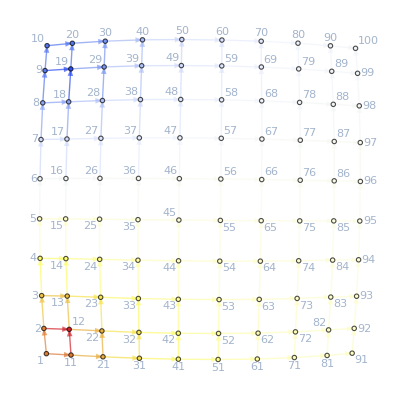

```mathematica
ColorNetworkByValueFunctionOperator[d2egrid][frmore]
```

```mathematica
vars = Join[Values[d2egrid["uvars"]],Values[d2egrid["jvars"]]];
{time,{{jtsystem,nojtrules},novariables}}=EliminateVars[{{system,rules},vars}]//AbsoluteTiming;
time
```

```mathematica
ColorNetworkByValueFunctionOperator[d2egrid][nojtrules]
MapThread[Rule,{vars,vars/.nojtrules}]
```

### Copy of the relevant functions

#### CleanEqualities

```mathematica
CleanEqualities[system_]:=
CleanEqualities[{system,{}}]
CleanEqualities[{system_,rules_}]:=
FixedPoint[EqEliminator,{system,rules}]
```

EqEliminator

```mathematica
EqEliminator[{True,rules_}]:=
{True,Simplify/@rules}
EqEliminator[{system_Or,rules_}]:=
{Simplify@system,Simplify/@rules}
EqEliminator[{system_GreaterEqual,rules_}]:=
{Simplify@system,Simplify/@rules}
EqEliminator[{system_LessEqual,rules_}]:=
{Simplify@system,Simplify/@rules}
EqEliminator[{system_Inequality,rules_}]:=
{Simplify@system,Simplify/@rules}
EqEliminator[{False,rules_}]:=
{False,rules}
EqEliminator[{system_,rules_List}]:=
EqEliminator[{system,Association[rules]}]
EqEliminator[{system_Equal,rules_Association}]:=
Module[{newrules},newrules=First@Solve[system];
newrules=Association[newrules];
{True,Join[rules/.newrules,newrules]}
]
EqEliminator[{system_And,rules_Association}]:=
Module[{EE,ON,newrules},(*separate equalities from the rest*)
EE=Select[system,(Head[#]===Equal)&];
If[EE===True,Return[{system,rules}]];
newrules=Solve[EE]//Quiet;(*The reason we use Quiet is:Solve::svars:Equations may not give solutions for all "solve" variables.*)
ON=Select[system,(Head[#]=!=Equal)&];
newrules=First@newrules;
newrules=Join[rules,Association@newrules];
{ON/.newrules,newrules/.newrules}
]
```

#### EliminateVars

```mathematica
EliminateVars[{{system_,rules_},vars_}]:=
FixedPoint[EliminateVarsStep,{{system,rules},vars}]
```

```mathematica
EliminateVarsStep[{{system_,rules_},vars_}]:=
Module[{var,subsys,subsyscomplement,position,newsys,newrules},var=SelectFirst[vars,!FreeQ[#][system]&];
Print[var];
If[Head[var]===Missing,
{{system,rules},{}},
position=First@FirstPosition[vars,var];
subsys=Select[system,Function[x,!FreeQ[var][x]]];
subsyscomplement=Select[system,Function[x,FreeQ[var][x]]];
subsys=Simplify[subsys];
newsys=subsys&&subsyscomplement;
{newsys,newrules}=CleanEqualities[{newsys,rules}];
{{newsys,newrules},Drop[vars,position]}
]
]
```

```mathematica
Variables
```

```mathematica
Solve[aa+bb+cc==0,{cc,bb}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{bb→-aa-cc}}